This notebook contains the tracking results of “Image 48”.

If the tracking in Python is not initialized correctly (see Functions -> Fast Marching -> Fast Marching Functions), uncomment the first line in this section.

Option 1: Calculate geodesics for image yourself: Execute section “4a. Calculate data for tracking” (takes a few hours)
Option 2: Load pre-calculated geodesics: Execute “4b. Load geodesics” (takes a few seconds)

# Tracking of Vascular Trees

```mathematica
SetDirectory[NotebookDirectory[]];
```

## 1. Functions

## 1.1. General functions

### Coordinate Conversion

```mathematica
(*Converts graphics coordinates to image coordinates using image dimensions*)
graphicsToImageCoordinates[imOrImDim_,coordinates_]:=Module[{ydim,xdim},If[Depth[imOrImDim]==2&&Length[imOrImDim]==2,{ydim,xdim}=imOrImDim,{ydim,xdim}=Dimensions[imOrImDim]];
Map[{ydim-#[[2]],#[[1]]}+1/2&,coordinates,{Depth[coordinates]-2}]]

(*Converts image coordinates to graphics coordinates using image dimensions*)
imageToGraphicsCoordinates[imOrImDim_,coordinates_]:=Module[{ydim,xdim},If[Depth[imOrImDim]==2&&Length[imOrImDim]==2,{ydim,xdim}=imOrImDim,{ydim,xdim}=Dimensions[imOrImDim]];
Map[{#[[2]],ydim+1-#[[1]]}-1/2&,coordinates,{Depth[coordinates]-2}]]

PointImageCoordinates[imOrImDim_,coordinates_]:=Module[{ydim,xdim},
Point[imageToGraphicsCoordinates[imOrImDim,coordinates]]]

LineImageCoordinates[imOrImDim_,coordinates_]:=Module[{ydim,xdim},
Line[imageToGraphicsCoordinates[imOrImDim,coordinates]]]

ArrowImageCoordinates[imOrImDim_,coordinates_]:=Module[{ydim,xdim},
Map[Arrow,imageToGraphicsCoordinates[imOrImDim,coordinates],{Depth[coordinates]-3}]]
```

## 1.2. Calculate Ground Truth Cost Function

### Finite Differences

These functions are taken and modified from OrientationScores`

#### All functions gathered (SE2FiniteDifferences is the main function)

```mathematica
SE2FiniteDifferences::usage="SE2FiniteDifferenceDerivative[os, order] calculates the left-invariant finite 
difference derivative of the orientation score. The order of the derivative is 
defined by \"order\". \"order\" is a string input containing the characters \"ξ\", 
\"η\" or \"θ\". For example, with order = \"ηη\" the second order derivative in 
η-direction is calculated.";
(*******************************************************)
(*****************************************Begin Private*)
Begin["Private`"];


(**********************************)
(***************Derivative kernels*)
(**********************************)




(******************************************Function for interpolation kernel*)


Options[InterpolationKernel]=Options[ListInterpolation];
InterpolationKernel[vector_,OptionsPattern[]]:=Module[{emptyKernel,kernelFinal,kernelOneElement,kernelOneElementInt,center},center=OptionValue[InterpolationOrder]+1;
emptyKernel=ConstantArray[0,{2*center-1,2*center-1}];
kernelFinal=emptyKernel;
Do[kernelOneElement=emptyKernel;
kernelOneElement[[i,j]]=1;
kernelOneElementInt=ListInterpolation[kernelOneElement,Method->OptionValue[Method],InterpolationOrder->OptionValue[InterpolationOrder]];
kernelFinal[[i,j]]=kernelOneElementInt[center+vector[[1]],center+vector[[2]]];,{i,1,2*center-1},{j,1,2*center-1}];
(*This result is a correlation kernel,we want a convolution kernel so we mirror the result:*)kernelFinal=Reverse[kernelFinal,{1,2}];
Return[kernelFinal]];


(******************************************Eta*)

(******Central*)
DηKernelCentral[θ_]:=DηKernelCentral[θ]=Module[{kernelPlus,kernelMin,kernel,eη},eη={-Sin[θ],Cos[θ]};
kernelPlus=InterpolationKernel[eη,Method->"Spline",InterpolationOrder->3];
kernelMin=InterpolationKernel[-eη,Method->"Spline",InterpolationOrder->3];
kernel=0.5 (kernelPlus-kernelMin);
Return[kernel]]
DηηKernelCentral[θ_]:=DηηKernelCentral[θ]=Module[{kernelPlus,kernelCenter,kernelMin,kernel,eη},eη={-Sin[θ],Cos[θ]};
kernelPlus=InterpolationKernel[eη,Method->"Spline",InterpolationOrder->3];
kernelCenter=InterpolationKernel[{0,0},Method->"Spline",InterpolationOrder->3];
kernelMin=InterpolationKernel[-eη,Method->"Spline",InterpolationOrder->3];
kernel=(kernelPlus-2*kernelCenter+kernelMin);
Return[kernel]]


(******Forward*)
DηKernelForward[θ_]:=DηKernelForward[θ]=Module[{kernelPlus,kernelMin,kernel,eη},eη={-Sin[θ],Cos[θ]};
kernelPlus=InterpolationKernel[eη,Method->"Spline",InterpolationOrder->3];
kernelMin=InterpolationKernel[{0,0},Method->"Spline",InterpolationOrder->3];
kernel=(kernelPlus-kernelMin);
Return[kernel]]
DηηKernelForward[θ_]:=DηηKernelForward[θ]=Module[{kernelPlus,kernelCenter,kernelMin,kernel,eη},eη={-Sin[θ],Cos[θ]};
kernelPlus=InterpolationKernel[2*eη,Method->"Spline",InterpolationOrder->3];
kernelCenter=InterpolationKernel[eη,Method->"Spline",InterpolationOrder->3];
kernelMin=InterpolationKernel[{0,0},Method->"Spline",InterpolationOrder->3];
kernel=(kernelPlus-2*kernelCenter+kernelMin);
Return[kernel]]



(******Backward*)
DηKernelBackward[θ_]:=DηKernelBackward[θ]=Module[{kernelPlus,kernelMin,kernel,eη},eη={-Sin[θ],Cos[θ]};
kernelPlus=InterpolationKernel[{0,0},Method->"Spline",InterpolationOrder->3];
kernelMin=InterpolationKernel[-eη,Method->"Spline",InterpolationOrder->3];
kernel=(kernelPlus-kernelMin);
Return[kernel]]
DηηKernelBackward[θ_]:=DηηKernelBackward[θ]=Module[{kernelPlus,kernelCenter,kernelMin,kernel,eη},eη={-Sin[θ],Cos[θ]};
kernelPlus=InterpolationKernel[{0,0},Method->"Spline",InterpolationOrder->3];
kernelCenter=InterpolationKernel[-eη,Method->"Spline",InterpolationOrder->3];
kernelMin=InterpolationKernel[-2*eη,Method->"Spline",InterpolationOrder->3];
kernel=(kernelPlus-2*kernelCenter+kernelMin);
Return[kernel]]



(******************************************Xi*)


(******Central*)
DξKernelCentral[θ_]:=DξKernelCentral[θ]=Module[{kernelPlus,kernelMin,kernel,eξ},eξ={Cos[θ],Sin[θ]};
kernelPlus=InterpolationKernel[eξ,Method->"Spline",InterpolationOrder->3];
kernelMin=InterpolationKernel[-eξ,Method->"Spline",InterpolationOrder->3];
kernel=0.5 (kernelPlus-kernelMin);
Return[kernel]]
DξξKernelCentral[θ_]:=DξξKernelCentral[θ]=Module[{kernelPlus,kernelMin,kernelCenter,kernel,eξ},eξ={Cos[θ],Sin[θ]};
kernelPlus=InterpolationKernel[eξ,Method->"Spline",InterpolationOrder->3];
kernelCenter=InterpolationKernel[{0,0},Method->"Spline",InterpolationOrder->3];
kernelMin=InterpolationKernel[-eξ,Method->"Spline",InterpolationOrder->3];
kernel=(kernelPlus-2*kernelCenter+kernelMin);
Return[kernel]]


(******Forward*)
DξKernelForward[θ_]:=DξKernelForward[θ]=Module[{kernelPlus,kernelMin,kernel,eξ},eξ={Cos[θ],Sin[θ]};
kernelPlus=InterpolationKernel[eξ,Method->"Spline",InterpolationOrder->3];
kernelMin=InterpolationKernel[{0,0},Method->"Spline",InterpolationOrder->3];
kernel=(kernelPlus-kernelMin);
Return[kernel]]
DξξKernelForward[θ_]:=DξξKernelForward[θ]=Module[{kernelPlus,kernelMin,kernelCenter,kernel,eξ},eξ={Cos[θ],Sin[θ]};
kernelPlus=InterpolationKernel[2*eξ,Method->"Spline",InterpolationOrder->3];
kernelCenter=InterpolationKernel[eξ,Method->"Spline",InterpolationOrder->3];
kernelMin=InterpolationKernel[{0,0},Method->"Spline",InterpolationOrder->3];
kernel=(kernelPlus-2*kernelCenter+kernelMin);
Return[kernel]]


(******Backward*)
DξKernelBackward[θ_]:=DξKernelBackward[θ]=Module[{kernelPlus,kernelMin,kernel,eξ},eξ={Cos[θ],Sin[θ]};
kernelPlus=InterpolationKernel[{0,0},Method->"Spline",InterpolationOrder->3];
kernelMin=InterpolationKernel[-eξ,Method->"Spline",InterpolationOrder->3];
kernel=(kernelPlus-kernelMin);
Return[kernel]]
DξξKernelBackward[θ_]:=DξξKernelBackward[θ]=Module[{kernelPlus,kernelMin,kernelCenter,kernel,eξ},eξ={Cos[θ],Sin[θ]};
kernelPlus=InterpolationKernel[{0,0},Method->"Spline",InterpolationOrder->3];
kernelCenter=InterpolationKernel[-eξ,Method->"Spline",InterpolationOrder->3];
kernelMin=InterpolationKernel[-2*eξ,Method->"Spline",InterpolationOrder->3];
kernel=(kernelPlus-2*kernelCenter+kernelMin);
Return[kernel]]





(**********************************)
(*************Derivative functions*)
(**********************************)


(******************************************Eta*)


LeftInvariantDerivativeDη[os_,periodicity_: π,coordinates_: "Matrix",method_:"Central"]:=Module[
{sφ,kernel,osOut},
sφ=periodicity/Length[os];
Table[Switch[method,"Central",If[coordinates=="Matrix",kernel=DηKernelCentral[sφ*(θi-1)];,kernel=DηKernelCentral[π/2-sφ*(θi-1)];];,"Forward",If[coordinates=="Matrix",kernel=DηKernelForward[sφ*(θi-1)];,kernel=DηKernelForward[π/2-sφ*(θi-1)];];,"Backward",If[coordinates=="Matrix",kernel=DηKernelBackward[sφ*(θi-1)];,kernel=DηKernelBackward[π/2-sφ*(θi-1)];];,_,(*If incorrectly specified then central*)If[coordinates=="Matrix",kernel=DηKernelCentral[sφ*(θi-1)];,kernel=DηKernelCentral[π/2-sφ*(θi-1)];]];
ListConvolve[kernel,os[[θi]],{-Ceiling[Dimensions[kernel]/2],Ceiling[Dimensions[kernel]/2]}],{θi,1,Length[os],1}]];
LeftInvariantDerivativeDηη[os_,periodicity_: π,coordinates_: "Matrix",method_:"Central"]:=Module[{sφ,kernel,osOut},sφ=periodicity/Length[os];
osOut=Table[Switch[method,"Central",If[coordinates=="Matrix",kernel=DηηKernelCentral[sφ*(θi-1)];,kernel=DηηKernelCentral[π/2-sφ*(θi-1)];];,"Forward",If[coordinates=="Matrix",kernel=DηηKernelForward[sφ*(θi-1)];,kernel=DηηKernelForward[π/2-sφ*(θi-1)];];,"Backward",If[coordinates=="Matrix",kernel=DηηKernelBackward[sφ*(θi-1)];,kernel=DηηKernelBackward[π/2-sφ*(θi-1)];];,_,(*If incorrectly specified then central*)If[coordinates=="Matrix",kernel=DηηKernelCentral[sφ*(θi-1)];,kernel=DηηKernelCentral[π/2-sφ*(θi-1)];]];
ListConvolve[kernel,os[[θi]],{-Ceiling[Dimensions[kernel]/2],Ceiling[Dimensions[kernel]/2]}],{θi,1,Length[os],1}];
Return[osOut]];





(******************************************Xi*)


LeftInvariantDerivativeDξ[os_,periodicity_: π,coordinates_:"Matrix",method_:"Central"]:=Module[{sφ,kernel,osOut},sφ=periodicity/Length[os];
Table[Switch[method,"Central",If[coordinates=="Matrix",kernel=DξKernelCentral[sφ*(θi-1)];,kernel=DξKernelCentral[π/2-sφ*(θi-1)];];,"Forward",If[coordinates=="Matrix",kernel=DξKernelForward[sφ*(θi-1)];,kernel=DξKernelForward[π/2-sφ*(θi-1)];];,"Backward",If[coordinates=="Matrix",kernel=DξKernelBackward[sφ*(θi-1)];,kernel=DξKernelBackward[π/2-sφ*(θi-1)];];,_,(*If incorrectly specified then central*)If[coordinates=="Matrix",kernel=DξKernelCentral[sφ*(θi-1)];,kernel=DξKernelCentral[π/2-sφ*(θi-1)];]];
ListConvolve[kernel,os[[θi]],{-Ceiling[Dimensions[kernel]/2],Ceiling[Dimensions[kernel]/2]}],{θi,1,Length[os],1}]
];
LeftInvariantDerivativeDξξ[os_,periodicity_: π,coordinates_:"Matrix",method_:"Central"]:=Module[{sφ,kernel,osOut},sφ=periodicity/Length[os];
osOut=Table[Switch[method,"Central",If[coordinates=="Matrix",kernel=DξξKernelCentral[sφ*(θi-1)];,kernel=DξξKernelCentral[π/2-sφ*(θi-1)];];,"Forward",If[coordinates=="Matrix",kernel=DξξKernelForward[sφ*(θi-1)];,kernel=DξξKernelForward[π/2-sφ*(θi-1)];];,"Backward",If[coordinates=="Matrix",kernel=DξξKernelBackward[sφ*(θi-1)];,kernel=DξξKernelBackward[π/2-sφ*(θi-1)];];,_,(*If incorrectly specified then central*)If[coordinates=="Matrix",kernel=DξξKernelCentral[sφ*(θi-1)];,kernel=DξξKernelCentral[π/2-sφ*(θi-1)];]];
ListConvolve[kernel,os[[θi]],{-Ceiling[Dimensions[kernel]/2],Ceiling[Dimensions[kernel]/2]}],{θi,1,Length[os],1}];
Return[osOut]];





(******************************************Theta*)


LeftInvariantDerivativeDθ[os_,periodicity_: π,coordinates_:"Matrix",method_:"Central"]:=Module[
{sφ},
sφ=periodicity/Length[os];
Switch[method,
"Central",
If[coordinates=="Matrix",1/(2) (RotateLeft[os,1]-RotateLeft[os,-1]),1/(2 sφ) (-RotateLeft[os,1]+RotateLeft[os,-1])]
,"Forward",
If[coordinates=="Matrix",(RotateLeft[os,1]-RotateLeft[os,0]), (-RotateLeft[os,0]+RotateLeft[os,-1])]
,"Backward",
If[coordinates=="Matrix",(RotateLeft[os,0]-RotateLeft[os,-1]), (-RotateLeft[os,1]+RotateLeft[os,0])]
,_,(*If incorrectly specified then central*)
If[coordinates=="Matrix",1/(2) (RotateLeft[os,1]-RotateLeft[os,-1]),1/(2 sφ) (-RotateLeft[os,1]+RotateLeft[os,-1])]
]
];
LeftInvariantDerivativeDθθ[os_,periodicity_: π,coordinate_:"Matrix",method_:"Central"]:=Module[
{sφ,osOut},
sφ=periodicity/Length[os];
Switch[method
,"Central",
If[coordinate=="Matrix",osOut=(RotateLeft[os,1]-2*RotateLeft[os,0]+RotateLeft[os,-1]);,osOut=1/(sφ^2) (RotateLeft[os,1]-2*RotateLeft[os,0]+RotateLeft[os,-1]);];
,"Forward",
If[coordinate=="Matrix",osOut=(RotateLeft[os,0]-2*RotateLeft[os,1]+RotateLeft[os,2]);,osOut=1/(sφ^2) (RotateLeft[os,0]-2*RotateLeft[os,-1]+RotateLeft[os,-2]);];
,"Backward",
If[coordinate=="Matrix",osOut=(RotateLeft[os,-2]-2*RotateLeft[os,-1]+RotateLeft[os,0]);,osOut=1/(sφ^2) (RotateLeft[os,2]-2*RotateLeft[os,1]+RotateLeft[os,0]);];
,_,(*If incorrectly specified then central*)
If[coordinate=="Matrix",osOut=(RotateLeft[os,1]-2*RotateLeft[os,0]+RotateLeft[os,-1]);,osOut=1/(sφ^2) (RotateLeft[os,1]-2*RotateLeft[os,0]+RotateLeft[os,-1]);];
];
Return[osOut]];










(**********************************)
(*******************Final function*)
(**********************************)



Options[SE2FiniteDifferences]={"Periodicity"->π,"CoordinateSystem"->"Matrix","Method"->"Central"};
SE2FiniteDifferences[os_,order_,OptionsPattern[]]:=Module[{osOut},Switch[order,"ξ",LeftInvariantDerivativeDξ[os,OptionValue["Periodicity"],OptionValue["CoordinateSystem"],OptionValue["Method"]],"ξξ",LeftInvariantDerivativeDξξ[os,OptionValue["Periodicity"],OptionValue["CoordinateSystem"],OptionValue["Method"]],"η",LeftInvariantDerivativeDη[os,OptionValue["Periodicity"],OptionValue["CoordinateSystem"],OptionValue["Method"]],"ηη",LeftInvariantDerivativeDηη[os,OptionValue["Periodicity"],OptionValue["CoordinateSystem"],OptionValue["Method"]],"θ",LeftInvariantDerivativeDθ[os,OptionValue["Periodicity"],OptionValue["CoordinateSystem"],OptionValue["Method"]],"θθ",LeftInvariantDerivativeDθθ[os,OptionValue["Periodicity"],OptionValue["CoordinateSystem"],OptionValue["Method"]],_String,osOut=os;
Do[Switch[StringTake[order,{i}],"ξ",osOut=LeftInvariantDerivativeDξ[osOut,OptionValue["Periodicity"],OptionValue["CoordinateSystem"],OptionValue["Method"]],"η",osOut=LeftInvariantDerivativeDη[osOut,OptionValue["Periodicity"],OptionValue["CoordinateSystem"],OptionValue["Method"]],"θ",osOut=LeftInvariantDerivativeDθ[osOut,OptionValue["Periodicity"],OptionValue["CoordinateSystem"],OptionValue["Method"]],_,Print["Warning!: character \""<>StringTake[order,{i}]<>"\" unknown. Charracters should be \"ξ\", \"η\" or \"θ\". Derivative skipped."]];,{i,1,StringLength[order],1}];
osOut,_,Print["Abort!: order should be specified as a string."]]];

End[];
```

### Orientation score transform

#### All functions directly copied (OrientationScoreTransform is the main function of interest)

```mathematica
CakeWaveletStack::usage="CakeWaveletStack[size,sφ] returns the set 
	of rotated wavelets with standard paramters (see Options[CakeWaveletStack]).
	The kernel stack has dimensions No x size x size, where No = \!\(\*FractionBox[\(sφ\), \(periodicity\)]\). 
	By default periodicity = π, meaning that the wavelets are constructed 
	from 0 to π. Parameter sφ specifies the angular resolution: 
	the number of kernels per π radians. 

Other parameters can be adjusted through the options or by calling the function 
	as follows:
 
CakeWaveletStack[size,sφ,kSpline,q,periodicity,ρInflection,kMn,σs,matrixCoordinatesQ].";

GaborWaveletStack::usage="GaborWaveletStack[a,sφ] returns the set 
	of rotated Gabor wavelets at scale a, with standard paramters (see Options[GaborWaveletStack]).
	The kernel stack has dimensions No x size x size, where No = \!\(\*FractionBox[\(sφ\), \(periodicity\)]\),
	and where size = 8*a*Sqrt[ϵ]. By default periodicity = π, meaning that 
	the wavelets are constructed from 0 to π. Parameter sφ specifies 
	the angular resolution: the number of kernels per π radians.";


WaveletTransform2D::usage="WaveletTransform2D[kernelStack,im] correlates each 
	kernel with the image. If the kernel dimensions and image dimensions 
	coincide, correlation is done using (conjugate) Fourier multiplication, else
	 it is done using correlation.";

OrientationScoreTransform::usage="OrientationScoreTransform[image, sφ] 
	constructs an orientation score from the image using cake wavelets with 
	default paramters (see Options[OrientationScoreTransform] and 
	?CakeWaveletStack). By default this is done through Fourier domain 
	multiplication, unless it is specified (by using the options) otherwise.";



(***********************************)
(******************CakeWaveletStack Private Functions*)

(*PolarCoordinateGridRadial returns a matrix in which each element gives the corresponding radial coordinate (with the origin in the center of the matrix*)
PolarCoordinateGridRadial=Compile[{{size,_Integer}},Table[Sqrt[x^2+y^2],{x,-((size-1)/2)-Mod[(size-1)/2,1],(size-1)/2-Mod[(size-1)/2,1]},{y,-((size-1)/2)-Mod[(size-1)/2,1],(size-1)/2-Mod[(size-1)/2,1]}]];
(*PolarCoordinateGridRadial returns a matrix in which each element gives the corresponding radial coordinate (with the origin in the center of the matrix*)
PolarCoordinateGridAngular=Compile[{{size,_Integer}},Table[Arg[x+I y],{x,-((size-1)/2)-Mod[(size-1)/2,1],(size-1)/2-Mod[(size-1)/2,1]},{y,-((size-1)/2)-Mod[(size-1)/2,1],(size-1)/2-Mod[(size-1)/2,1]}]];
(*MnWindow gives the radial windowing matrix for sampling the fourier domain*)
MnWindow=Compile[{{size,_Integer},{n,_Integer},{ρinflection,_Real}},Module[{ρMatrix},ρMatrix=$MachineEpsilon+1/Sqrt[(2*ρinflection^2)/(1+2 n)] PolarCoordinateGridRadial[size];
Total[Table[E^-ρMatrix^2*ρMatrix^(2k)/k!,{k,0,n}]]],{{k!,_Real}}];
(*BSplineScalarFunc is a compile spline basis function of arbitrary order.The function is defined for scalars,list and 2D matrix objects*)
BSplineScalarFunc=Compile[{{n,_Integer},{x,_Real}},Module[{function,intervalCheck},Total[Table[function=1/(2 (n+1-1)!) Total[Table[Binomial[n+1,k](x+(n+1)/2-k)^(n+1-1) (-1)^k Sign[i+(n+1)/2-k],{k,0,n+1}]];
intervalCheck=Round[If[i<(n+1-1)/2,UnitStep[x-(i-1/2+$MachineEpsilon)]*UnitStep[-(x-(i+1/2))],UnitStep[x-(i-1/2+$MachineEpsilon)]*UnitStep[-(x-(i+1/2-$MachineEpsilon))]]];
function*intervalCheck,{i,(1-n-1)/2,(n-1+1)/2}]]]];
BSplineListFunc=Compile[{{n,_Integer},{x,_Real,1}},Module[{function,intervalCheck},Total[Table[function=1/(2 (n+1-1)!) Total[Table[Binomial[n+1,k](x+(n+1)/2-k)^(n+1-1) (-1)^k Sign[i+(n+1)/2-k],{k,0,n+1}]];
intervalCheck=Round[If[i<(n+1-1)/2,UnitStep[x-(i-1/2+$MachineEpsilon)]*UnitStep[-(x-(i+1/2))],UnitStep[x-(i-1/2+$MachineEpsilon)]*UnitStep[-(x-(i+1/2-$MachineEpsilon))]]];
function*intervalCheck,{i,(1-n-1)/2,(n-1+1)/2}]]]];
BSplineMatrixFunc=Compile[{{n,_Integer},{x,_Real,2}},Module[{function,intervalCheck},Total[Table[function=1/(2 (n+1-1)!) Total[Table[Binomial[n+1,k](x+(n+1)/2-k)^(n+1-1) (-1)^k Sign[i+(n+1)/2-k],{k,0,n+1}]];
intervalCheck=Round[If[i<(n+1-1)/2,UnitStep[x-(i-1/2+$MachineEpsilon)]*UnitStep[-(x-(i+1/2))],UnitStep[x-(i-1/2+$MachineEpsilon)]*UnitStep[-(x-(i+1/2-$MachineEpsilon))]]];
function*intervalCheck,{i,(1-n-1)/2,(n-1+1)/2}]]]];
(*WindowGauss retuns the spatial Gauss envelope*)
WindowGauss=Compile[{{size,_Integer},{σs,_Real}},Table[E^(-(x^2/(2σs^2))-y^2/(2σs^2)),{x,-((size-1)/2)-Mod[(size-1)/2,1],(size-1)/2-Mod[(size-1)/2,1]},{y,-((size-1)/2)-Mod[(size-1)/2,1],(size-1)/2-Mod[(size-1)/2,1]}]];
(*CakeWaveletStackFourier constructs the cake wavelets in the Fourier domain (note that windowing in the spatial domain is still required after this*)
CakeWaveletStackFourier=Compile[{{size,_Integer},{sφ,_Real},{kspline,_Integer},{q,_Integer},{ρInflection,_Real},{kMn,_Integer},{matrixCoordinatesQ,True|False}},Module[{mnWindow,angleGrid},mnWindow=MnWindow[size,kMn,ρInflection];
angleGrid=PolarCoordinateGridAngular[size];
Table[mnWindow*BSplineMatrixFunc[kspline,If[matrixCoordinatesQ,Mod[angleGrid-θ-π/2,2π,-π]/sφ,Mod[angleGrid+θ+π,2π,-π]/sφ]],{θ,π,2π-sφ/q,(sφ/q)}]]];
(*ErfSet retuns a set of 2D error functions.This function is used to cut the wavelets in two (in the spatial domain)*)
ErfSet=Compile[{{size,_Real},{No,_Integer}},Module[{dθ},Table[Table[1/2 (1+Erf[x Cos[(2 (-1+i) π)/No]+y Sin[(2 (-1+i) π)/No]]),{x,-((size-1)/2)-Mod[(size-1)/2,1],(size-1)/2-Mod[(size-1)/2,1]},{y,-((size-1)/2)-Mod[(size-1)/2,1],(size-1)/2-Mod[(size-1)/2,1]}],{i,1,No}]]];








(***********************************)
(******************CakeWaveletStack*)

Options[CakeWaveletStack]={"SplineOrder"->3,"AngularSubSampleRate"->1,"Periodicity"->π,"InflectionPoint"->"Automatic","MnOrder"->8,"GaussianWindowSigma"->"Automatic","InflectionPoint"->"Automatic","CoordinateSystem"->"Matrix","SingleVsDoubleSided"->"Double"};
(*Function definition for direct options input*)
CakeWaveletStack[size_,sφ_,kSpline_,q_,periodicity_,ρInflection_,kMn_,σs_,matrixCoordinatesQ_,singleOrDouble_]:=Module[{cakeF,cakeIF,window,cake},
cakeF=CakeWaveletStackFourier[size,sφ,kSpline,q,ρInflection,kMn,matrixCoordinatesQ];
(*cakeF[[All,Ceiling[(size-1)/2]+2,Ceiling[(size-1)/2]+2]]=0*sφ/periodicity;(*The central frequency overlaps with all rotated kernels,it should still ad up to 1*)*)s=2;
cakeF[[All,Ceiling[(size-1)/2]+1-s;;Ceiling[(size-1)/2]+1+s,Ceiling[(size-1)/2]+1-s;;Ceiling[(size-1)/2]+1+s]]=sφ/periodicity;(*The central frequency overlaps with all rotated kernels,it should still ad up to 1*)cakeIF=RotateRight[InverseFourier[RotateLeft[#,Floor[{size,size}/2]]],Floor[{size,size}/2]]&/@cakeF;
window=WindowGauss[size,σs];
cake=window*#&/@cakeIF;
If[periodicity==2π,cake=Flatten[{cake,Conjugate[Reverse[Reverse[#]]&/@cake]},1];];
If[singleOrDouble=="Single",cake=cake*ErfSet[size,q*periodicity/sφ];];
Return[cake]];
(*Function definition that uses the OptionsPattern*)
CakeWaveletStack[size_,sφ_,OptionsPattern[]]:=Module[{kSpline,q,periodicity,ρInflection,kMn,σs,matrixCoordinatesQ,cakeStack,singleOrDouble},(****************************)(***********Check Parameters*)kSpline=OptionValue["SplineOrder"];
q=OptionValue["AngularSubSampleRate"];
periodicity=OptionValue["Periodicity"];
Switch[OptionValue["InflectionPoint"],"Automatic",ρInflection=(size-1)/2 0.8;,_,ρInflection=OptionValue["InflectionPoint"]];
kMn=OptionValue["MnOrder"];
Switch[OptionValue["GaussianWindowSigma"],"Automatic",σs=(size-1)/4;,_,σs=OptionValue["GaussianWindowSigma"]];
If[OptionValue["CoordinateSystem"]=="Matrix",matrixCoordinatesQ=True,matrixCoordinatesQ=False];
singleOrDouble=OptionValue["SingleVsDoubleSided"];
(***************************)(***********Construct Stack*)cakeStack=CakeWaveletStack[size,sφ,kSpline,q,periodicity,ρInflection,kMn,σs,matrixCoordinatesQ,singleOrDouble];
Return[cakeStack]];








(***********************************)
(******************GaborWaveletStack*)

Options[GaborWaveletStack]={"ϵ"->4,"KernelSize"->"Automatic","k0"->{0,3},"Periodicity"->π,"SingleVsDoubleSided"->"Double","CoordinateSystem"->"Matrix"};
GaborWaveletStack[a_,sφ_,OptionsPattern[]]:=Module[{ϵ,A,k0,size,periodicity,stack,singleOrDouble,matrixCoordinatesQ},(*Parameters:*)ϵ=OptionValue["ϵ"];
A=({{ϵ^(-1/2),0},{0,1}});
k0=OptionValue["k0"];
Switch[OptionValue["KernelSize"],"Automatic",size=Floor[8*Sqrt[ϵ]*a],_Integer,size=OptionValue["KernelSize"],_,size=Floor[8*Sqrt[ϵ]*a]];
If[EvenQ[size],size=size+1];
periodicity=OptionValue["Periodicity"];
singleOrDouble=OptionValue["SingleVsDoubleSided"];
matrixCoordinatesQ=OptionValue["CoordinateSystem"]=="Matrix";
(*The stack:*)stack=GenerateKernelSetGabor[A,k0,a,Round[π/sφ],size,matrixCoordinatesQ];
If[periodicity==2 π,stack=Flatten[{stack,Conjugate[Reverse[Reverse[#]]&/@stack]},1];];
If[singleOrDouble=="Single",stack=stack*ErfSet[size,periodicity/sφ];];
Return[stack]];
GenerateKernelSetGabor=Compile[{{A,_Real,2},{k0,_Real,1},{a,_Real},{nθ,_Real},{dim,_Real},{matQ,True|False}},Module[{dθ},dθ=(π)/nθ;
0.00000000001+(1/((4 a π)/E^(9/2)))(1/a)*Table[Table[With[{xx={Cos[-θ+π/2],-Sin[-θ+π/2]}.{x,y},yy={Sin[-θ+π/2],Cos[-θ+π/2]}.{x,y}},Exp[I (k0.({yy,xx}/a))]Exp[-(1/2) Norm[(A.({yy,xx}/a))]^2]],{x,-Floor[dim/2],Floor[dim/2]-(1-2*Mod[dim/2,1])},{y,-Floor[dim/2],Floor[dim/2]-(1-2*Mod[dim/2,1])}],{θ,If[matQ,π,π+π/2],If[matQ,2*π-dθ,+π/2+dθ],If[matQ,dθ,-dθ]}]]];










(***********************************)
(****************WaveletTransform2D*)

WaveletTransform2D[kernels_,im_,fourierQ_:1]:=Module[{imF,kernelsF,os,dimkernelx1,dimkernely1,dimkernelx2,dimkernely2},If[Dimensions[kernels][[-2;;-1]]==Dimensions[im]&&fourierQ==1,(*Using the Fourier transform*)imF=Fourier[im];
kernelsF=Fourier[Reverse[#,{1,2}]]&/@kernels;
os=RotateRight[InverseFourier[#*imF],Ceiling[0.1+Dimensions[im]/2]]&/@kernelsF;,(*Using Correlation*){dimkernelx1,dimkernely1}=Dimensions[kernels[[1]]]/2//Ceiling;
{dimkernelx2,dimkernely2}=Dimensions[kernels[[1]]];
If[EvenQ[dimkernelx2],dimkernelx2=dimkernelx2/2+1,dimkernelx2=dimkernelx2/2//Ceiling];
If[EvenQ[dimkernely2],dimkernely2=dimkernely2/2+1,dimkernely2=dimkernely2/2//Ceiling];
os=Table[ListCorrelate[kernels[[i]],im,{{-dimkernelx1,-dimkernely1},{dimkernelx2,dimkernely2}}],{i,1,Length[kernels],1}]];
Return[os]];












(***********************************)
(****************WaveletTransform2D*)

Options[OrientationScoreTransform]={"WaveletSize"->151,"SplineOrder"->3,"AngularSubSampleRate"->1,"Periodicity"->π,"InflectionPoint"->"Automatic","MnOrder"->8,"GaussianWindowSigma"->"Automatic","InflectionPoint"->"Automatic","CoordinateSystem"->"Matrix","SingleVsDoubleSided"->"Double","Method"->"SpatialConvolution"};

OrientationScoreTransform::dim="Warning! Method \"Fourier\" can not be used if the image dimensions are not equal. Convolution based method with kernel size `1`x`1` used instead.";
OrientationScoreTransform::size="Warning! Wavelet size can not be specified with method \"Fourier\", size is set equal to the image size.";

OrientationScoreTransform[im_,sφ_,OptionsPattern[]]:=Module[{dimx,dimy,size,kSpline,q,periodicity,ρInflection,kMn,σs,matrixCoordinatesQ,cakeStack,os,singleOrDouble},(****************************)(***********Check Parameters*){dimx,dimy}=Dimensions[im][[1;;2]];
If[OptionValue["Method"]=="Fourier",If[dimx≠dimy,Message[OrientationScoreTransform::dim,OptionValue["WaveletSize"]];
size=OptionValue["WaveletSize"];,If[OptionValue["WaveletSize"]≠Options[OrientationScoreTransform,"WaveletSize"][[1,2]],Message[OrientationScoreTransform::size];];
size=dimx;],size=OptionValue["WaveletSize"]];
kSpline=OptionValue["SplineOrder"];
q=OptionValue["AngularSubSampleRate"];
periodicity=OptionValue["Periodicity"];
Switch[OptionValue["InflectionPoint"],"Automatic",ρInflection=(size-1)/2 0.8;,_,ρInflection=OptionValue["InflectionPoint"]];
kMn=OptionValue["MnOrder"];
Switch[OptionValue["GaussianWindowSigma"],"Automatic",σs=(size-1)/4;,_,σs=OptionValue["GaussianWindowSigma"]];
If[OptionValue["CoordinateSystem"]=="Matrix",matrixCoordinatesQ=True,matrixCoordinatesQ=False];
singleOrDouble=OptionValue["SingleVsDoubleSided"];
(***************************)(***********Construct Stack*)cakeStack=CakeWaveletStack[size,sφ,kSpline,q,periodicity,ρInflection,kMn,σs,matrixCoordinatesQ,singleOrDouble];
os=WaveletTransform2D[cakeStack,im,If[OptionValue["Method"]=="Fourier",1,0]];
Return[os]];
```

### ITKFM method

```mathematica
<<NIfTIParser`
```

This is a beta version. Send any bug reports to: T.C.J.Dela.Haije@student.tue.nl
If applicable please include the files that resulted in errors.

#### Construct metric

```mathematica
SE2ConstructMetric=Compile[{{No,_Integer},{Nx,_Integer},{Ny,_Integer},{sθ,_Real},{μ,_Real},{ϵ,_Real}},
Transpose[
Table[
With[{θ=(i-1)*sθ},
ConstantArray[{{μ^2 Cos[θ]^2+ϵ^2 μ^2 Sin[θ]^2,μ^2 Cos[θ] Sin[θ]-1. ϵ^2 μ^2 Cos[θ] Sin[θ],ϵ^2 μ^2 Cos[θ]^2+μ^2 Sin[θ]^2,0.,0.,1. sθ^2}},{Nx,Ny}]
]
,{i,1,No,1}]
,{3,1,2,4,5}]
];
```

#### Fast marching

```mathematica
SRWaveFrontPropagationITKFM[cost_,g0dIn_,g1dIn_,μ_,ϵ_,sTheta_,sx_]:=Module[{
No,Nx,Ny,
metric,
g0d,g1d,exportList,
header,
hed,W,itkfmPath,
geodesicPath
},

{No,Nx,Ny}=Dimensions[cost];

(***************Construct metric*)
metric=SE2ConstructMetric[No,Nx,Ny,sTheta,μ,ϵ];
metric=Transpose[cost^2,{3,1,2}]*metric;
(*Pad metric (cyclic boundary conditions theta direction)*)
metric=Transpose[Flatten[{#,#,#},1],{3,1,2,4,5}]&@Transpose[metric,{2,3,1,4,5}];


(***************Input check - Source and sink point*)
(*Source point(s) check (always work with a list of seed points)*)
If[(*If only one seed point is provided*)
Dimensions[g0dIn]=={3}
,
g0d={g0dIn}
,(*if a list is provided:*)
g0d=g0dIn;
];
(*Sink point(s)*)
If[(*If sink point is not specified (0)*)
ToString[N[g1dIn]]==ToString[0.]
,(*Then place sink at the corner of the image*)
g1d=Dimensions[cost]
,
(*Check for list of seed points*)
If[(*If only one sink point is specified*)
Dimensions[g1dIn]=={3}
,(*Then make a list of sink points out of it*)
g1d={g1dIn}
,(*Otherwise copy the list of sink points*)
g1d=g1dIn];
];
(*g0d=Union[g0d];(*Remove duplicates*)*)
(*g1d=Union[g1d];(*Remove duplicates*)*)



(***************Export seed point*)
If[(*only 1 sink point is provided*)
Length[g1d]==1,(*Then only one end point is provided*)
exportList={{g0d⟦1,2⟧,g0d⟦1,3⟧,g0d⟦1,1⟧+No},{g1d⟦1,2⟧,g1d⟦1,3⟧,g1d⟦1,1⟧+No}};(*Prepend the first seed point*)
Export["_tmp_sourcesink.txt",exportList-1,"Table","FieldSeparators"->" "];
,
exportList={{g0d⟦1,2⟧,g0d⟦1,3⟧,g0d⟦1,1⟧+No}};(*Prepend the first seed point*)
Do[AppendTo[exportList,{g1d⟦i,2⟧,g1d⟦i,3⟧,g1d⟦i,1⟧+No}],{i,1,Length[g1d],1}];
Export["_tmp_sourcesink.txt",exportList-1,"Table","FieldSeparators"->" "]
];
If[(*More then one source point is provided*)
Length[g0d]≠1
,(*Than Export additional seed point file*)
exportList=Table[{g0d⟦i,2⟧,g0d⟦i,3⟧,g0d⟦i,1⟧+No},{i,1,Length[g0d],1}];
Export["_tmp_extraseeds.txt",exportList-1,"Table","FieldSeparators"->" "]
];


(***************Export volume*)
header={{348,"","",0,0,"r",{0,0,0},{5,11,11,11,1,6,0,0},0.,0.,0.,1005,16,32,0,{0.,1.,1.,1.,1.,1.,0.,0.},352.,0.,0.,0,0,{2,8},0.,0.,0.,0.,0,0,"","",0,0,0.,0.,0.,0.,0.,0.,{1.,0.,0.,0.},{0.,1.,0.,0.},{0.,0.,1.,0.},"","n+1",{0,0,0,0}}};
header⟦1,8,2;;6⟧=(metric//Dimensions);
header⟦1,16,2⟧=1.;(*scaling x dimension*)
header⟦1,16,3⟧=1.;(*scaling y dimension*)
header⟦1,16,4⟧=1.;(*scaling theta dimension*)
(*Export volume*)
ExportNIfTI["_tmp_metric.nii",{header,metric},AutoOverwrite->True];


(**************Solve Eikonal equation, by running ITKFM.exe from command propmpt ($SystemSHell)*)
(*itkfmPath="\""<>NotebookDirectory[]<>"ITKFM_win64\\ITKFM\"";*)
itkfmPath=FileNameJoin[{NotebookDirectory[],"ITKFM_"<>$SystemID,"ITKFM"}];
If[(*Only one seed point is provided*)
Length[g0d]==1
,(*Then*)
itkfmlog=RunProcess[$SystemShell,All,itkfmPath<>" _tmp_metric.nii _tmp_sourcesink.txt _tmp_path.txt _tmp_W.nii
exit
"];
,(*Otherwise*)
itkfmlog=RunProcess[$SystemShell,All,itkfmPath<>" _tmp_metric.nii _tmp_sourcesink.txt _tmp_path.txt _tmp_W.nii _tmp_extraseeds.txt
exit
"];
];




(*************Read in results*)
{hed,W}=ImportNIfTI["_tmp_W.nii"];
W=MapThread[Min[#1,#2,#3]&,{W⟦All,All,1;;No⟧,W⟦All,All,No+1;;2*No⟧,W⟦All,All,2*No+1;;3*No⟧},3];
W=Transpose[W,{2,3,1}];

If[Length[g1d]==1,(*Then only one end point is provided*)
geodesicPath=Import["_tmp_path.txt","Data"]+1;
geodesicPath={Reverse@geodesicPath⟦All,{3,1,2}⟧};
,
geodesicPath=Table[
geodesicPath=Import["_tmp_path_"<>ToString[i]<>".txt","Data"]+1;
DeleteFile["_tmp_path_"<>ToString[i]<>".txt"];(*Delete file after reading in the data*)
Reverse@geodesicPath⟦All,{3,1,2}⟧
,{i,1,Length[g1d],1}];
];
geodesicPath⟦All,All,1⟧=geodesicPath⟦All,All,1⟧-No;


(************Clean working directory*)
DeleteFile["_tmp_sourcesink.txt"];
DeleteFile["_tmp_metric.nii"];
DeleteFile["_tmp_path.txt"];
Quiet[DeleteFile["_tmp_path_"<>ToString[Length[g1d]+1]<>".txt"];];
DeleteFile["_tmp_W.nii"];
If[Length[g0d]≠1,DeleteFile["_tmp_extraseeds.txt"]];

(*Return output*)
Return[{W,geodesicPath}]
];
```

## 1.3 TV-Flow Enhancement

```mathematica
DoLeftTVF[os_,α_, t_, dt_, Ds_, Da_, source_, κ_:1] := Module[
{out = os, progress=0.0, diff, grad, grad1, grad2, grad3, gradNorm, gradGN1, gradGN2, gradGN3, gradGN,λ=50, L1, L2, img=InverseOrientationScoreTransform[os]},
Monitor[
L1 = {ImageDistance[source, img, DistanceFunction->ManhattanDistance]};
L2 = {ImageDistance[source, img, DistanceFunction->EuclideanDistance]};
out = Affix[out, "Data"-> λ * out["Data"]];
Do[
grad = OrientationScoreTensor[out, "Gradient"]["Data"];
grad1 = Ds*grad⟦All,All,All,1⟧;
grad2 = Ds*κ^2*grad⟦All,All,All,2⟧;
grad3 = Da*grad⟦All,All,All,3⟧;
gradNorm = Sqrt[grad1^2/Ds+grad2^2/(Ds*κ^2)+grad3^2/Da+0.001^2];

gradNorm = GaussianFilter[gradNorm, {{1,1,0}}, Padding->"Fixed"];
gradNorm = GaussianFilter[gradNorm, {{0,0,1/2}}, Padding-> "Periodic"];

gradGN1 = OrientationScoreTensor[Affix[out, "Data"-> grad1/gradNorm], "Gradient"]["Data"];
gradGN2 = OrientationScoreTensor[Affix[out, "Data"-> grad2/gradNorm], "Gradient"]["Data"];
gradGN3 = OrientationScoreTensor[Affix[out, "Data"-> grad3/gradNorm], "Gradient"]["Data"];

gradGN = MapThread[{#1,#2,#3}&,{gradGN1, gradGN2, gradGN3},4];

diff = (gradGN⟦All,All,All,1,1⟧
+α*gradGN⟦All,All,All,2,2⟧
+α*gradGN⟦All,All,All,3,3⟧);

out = Affix[out, "Data"-> out["Data"] + dt*diff];
img = InverseOrientationScoreTransform[Affix[out, "Data"-> (out["Data"]/λ)]];
AppendTo[L1, ImageDistance[source, img, DistanceFunction->ManhattanDistance]];
AppendTo[L2, ImageDistance[source, img, DistanceFunction->EuclideanDistance]];
progress += dt/t;
, Round[t/dt]
];
, {ProgressIndicator[progress],
Image[img, ImageSize->800]}];
Return[{Affix[out, "Data"-> (out["Data"]/λ)],L1,L2}];
];
```

## 1.4. Data-Driven Frame (Gauge Frame)

Gauge frames are expressed w.r.t. the left invariant frame.

### Lie Analysis Package

```mathematica
$HistoryLength=1;
<< LieAnalysis`
```

#### General subroutines

Transform Hessian matrix from left invariant frame to a gauge frame.

```mathematica
HessianToGaugeFrame=Compile[{{tensor,_Real,2},{gaugeFrame,_Real,2}},gaugeFrameᵀ.tensor.gaugeFrame,RuntimeAttributes->{Listable}];
```

#### Gauge Frame

Returns a matrix field gf that contains the coefficients of the gauge frame s.t.

ℬ_i=∑_(j=1)^3 gf⟦i,j⟧𝒜_j
j=1  spatial, j=2 orthogonal spatial, j=3 angular
gf is a  list that is output of the function below 
Output is an array with entries Nx,Ny,Nθ, 3,3

Function to calculate other version of gauge frame.

```mathematica
CalcGaugeFrame[os_,ξ_,ζ_,σsHess_,σaHess_,σsExt_:0,σaExt_:0]:=Module[
{H,M,A,B1,χ,ν,B2,B3},
(*os=ObjPositionOrientationData[{"Data"->osData,"Symmetry"->π, "Wavelets"-> None, "InputData"-> None, "DcFilteredImage"->0}];*)
(* obtain the Hessian field *)
H=OrientationScoreTensor[os,{σsHess,σaHess},"Hessian"]["Data"];
H=H/Max[Abs[H]];
(* blur the Hessian field *)
If[{σsExt,σaExt} =!= {0,0},
H = LieAnalysis`Common`ExternalRegularization[H, os["FullOrientationList"], {σsExt,σaExt}];
];
(* define M *)
M = DiagonalMatrix[{1/ξ,ζ/ξ,1}];  (*Bekijken wat verschil is met ζ en 1*)(*M is already inversed compared to theory*)
(* solve the optimization problem (i.e. fit B1) *)
A=Map[(M^2).(#ᵀ.(M^2).#)&,H,{3}];
B1=Map[(Eigenvectors[#,Method->"Direct"]⟦3⟧)&,A,{3}];
(* multiply B1 by the sign of Subscript[(B1), 1] s.t. it points in the same direction as A1 *)
B1=Map[Sign[#⟦1⟧]*#&,B1,{3}];
(* obtain angles representing deviation of horizontality and curvature *)
B1=Map[If[#⟦1⟧==0&&#⟦2⟧==0,{1,0,0},#]&,B1,{3}];
(*When the direction of B1 is purely angular, it is replaced by the Left Invariant Frame*)

χ=Map[ArcTan[#⟦1⟧,#⟦2⟧]&,B1,{3}];(*arctan(Subscript[B1, 1]/Subscript[B1, 2])*)
ν=Map[ArcTan[√((#⟦1⟧)^2+(#⟦2⟧)^2),#⟦3⟧]&,B1,{3}];
Print[MinMax[Cos[ν]]];
(* normalize *)
B1=Map[# /√((ξ #⟦1⟧)^2+(ξ/ζ#⟦2⟧)^2+(#⟦3⟧)^2)&,B1,{3}]; 
(* calculate B2 *)
B2=MapThread[{-Sin[#1],Cos[#1],0}&,{χ,ν},3];
B2=Map[# /√((ξ #⟦1⟧)^2+(ξ/ζ#⟦2⟧)^2+(#⟦3⟧)^2)&,B2,{3}]; (* normalize *)
(* calculate B3 *)
B3=MapThread[{-Cos[#1]Sin[#2],-Sin[#1]Sin[#2],Cos[#2]}&,{χ,ν},3];
B3=Map[# /√((ξ #⟦1⟧)^2+(ξ/ζ#⟦2⟧)^2+(#⟦3⟧)^2)&,B3,{3}]; (* normalize *)
Return[Transpose[{B1,B2,B3},{4,1,2,3,5}]]
]
```

Function to calculate data-driven term (Hessian)

```mathematica
CalcGaugeFrameNew2[os_,ξ_,ζ_,σsHess_,σaHess_,σsExt_:0,σaExt_:0]:=Module[
{H,M,A,B1,χ,ν,B2,B3},
(* obtain the Hessian field *)
H=OrientationScoreTensor[os,{σsHess,σaHess},"Hessian"]["Data"];
H=H/Max[Abs[H]];
(* blur the Hessian field *)
If[{σsExt,σaExt} =!= {0,0},
H = LieAnalysis`Common`ExternalRegularization[H, os["FullOrientationList"], {σsExt,σaExt}];
];
Return[H]
]
```

Function to calculate data - driven term (Structure tensor)

```mathematica
CalcGaugeFrameNewStructureTensor[os_,ξ_,ζ_,σsHess_,σaHess_,σsExt_:0,σaExt_:0]:=Module[
{H,M,A,B1,χ,ν,B2,B3},
(* obtain the structure tensor field *)
H=OrientationScoreTensor[os,{σsHess,σaHess},"StructureTensor"]["Data"];
H=H/Max[Abs[H]];
(* blur the Hessian field *)
If[{σsExt,σaExt} =!= {0,0},
H = LieAnalysis`Common`ExternalRegularization[H, os["FullOrientationList"], {σsExt,σaExt}];
];
Return[H]
]
```

#### Iterated stabilization

Iteratively fits gauge frames to (the data of) an orientation score. Returns the final gauge frame and corresponding orientation confidence.

```mathematica
StabilizeGFandOC[U_,iterations_,ξ_,ζ_,σs_,σa_]:=Module[{obj,gf,hess,hessLIFscaled,hessGf,oc,i,M},
oc=U;
M = DiagonalMatrix[{1/ξ,ζ/ξ,1}];
For[i=0,i<iterations,i++,
obj=ObjPositionOrientationData[{"Data"->oc,"Symmetry"->2π, "Wavelets"-> None, "InputData"-> None, "DcFilteredImage"->0}]; (*Important for subsequent functions we need object structure "Obl....Data" not just an array*)
gf=CalcGaugeFrame[obj,ξ,ζ,σs,σa];
hess = OrientationScoreTensor[obj, {σs,σa}, "Hessian"]["Data"];
hessLIFscaled=Map[M.#.M&,hess,{3}]; (*converting the Hessian to the new LIF frame*)
hessGf = HessianToGaugeFrame[hessLIFscaled, gf];
oc =-(hessGf⟦All,All,All,2,2⟧+hessGf⟦All,All,All,3,3⟧); (*B22+B33*)
oc=Clip[oc,{0,∞}];
oc=oc/Max[oc];
];
(*gf=Map[#/(√((#⟦1⟧)^2+(#⟦2⟧)^2+(#⟦3⟧)^2))&,gf,{3}];(*normalize*)*)

Return[{gf,oc}]
]
```

#### Visualization of Gauge Frame

Exponential curve through a point (x,y,θ) (at t = 0) with speed expressed by coordinate vector (c_1,c_2,c_3) in the left invariant frame.

```mathematica
expCurve[{x_,y_,θ_},{c1_,c2_,c3_},t_]:=If[c3==0.0,
{x+Cos[θ]c1 t-Sin[θ]c2 t,y+Sin[θ]c1 t+Cos[θ]c2 t,θ},
{x+1/c3(Cos[θ](c1 Sin[c3 t]+c2(Cos[c3 t]-1))-Sin[θ](c1(1-Cos[c3 t])+c2 Sin[c3 t])),
y+1/c3(Sin[θ](c1 Sin[c3 t]+c2(Cos[c3 t]-1))+Cos[θ](c1(1-Cos[c3 t])+c2 Sin[c3 t])),
θ+c3 t}
]
```

```mathematica
(*expCurveA[{x_,y_,θ_},t_]:={x+t*Cos[θ],y+t*Sin[θ],θ}*)
```

Reference: Lecture Notes DGIP Part I: Remark 9, Definition 4

Shows projections of  exponential curves with velocity given by  the first gauge vector at several random positions.
Points are selected in the xy-plane, for θ the coordinate with maximum orientation confidence is selected.

```mathematica
PlotGaugeFrameFGThinLines[oc_,gf_,positions_,numSamples_,length_,baseImage_]:=Module[{xyList,θdList,θList,cList,gdList,gList,Nx,Ny,Nθ,sθ},
{Nx,Ny,Nθ}=Dimensions[oc];
sθ=2 π/Nθ;
xyList=RandomSample[positions,numSamples];  (* selection of a number of samples, now Random later adapt if needed*)
θdList=Ordering[Abs[oc⟦Sequence@@#⟧],-1]⟦1⟧&/@xyList; (* Select θ-component with maximum abs value in orientation confidence, label d= "discrete" *)
gdList=Transpose[Flatten[{Transpose[xyList],{θdList}},1]]; (* Put everything together x-y-θ-coord*)
θList=(θdList-1)sθ;                                        (* convert to continuous coordinates so that exponential curve formulas can be used *)
gList=Transpose[Flatten[{Transpose[xyList],{θList}},1]];  (* Put everything together in continuous x-y-θ-coord*)
cList=gf⟦Sequence@@#,1⟧&/@gdList; (* Pul first row from the gf list so this gives the first gauge vector field in discrete coordinates*)
Show[
baseImage,
(*Convert coordinates to image coordinates x and y axes are flipped, this causes rotation direction to reverse*)
Table[
ParametricPlot[{#⟦2⟧-0.5,Nx-#⟦1⟧+0.5}&@expCurve[gList⟦i⟧,cList⟦i⟧,t],{t,-length/2,length/2},PlotStyle->{Thickness[0.004],Orange}]
,{i,1,Length[gList],1}],
ImageSize->800
]
]
```

Explanation input variables: in above routine: oc = orientation confidence, gf = gaugeframe (discrete) coordinatelist, positions = list of spatial coordinates where you want to have the plot, numsamples = number of arcs to be visualized, length = tmax in continuous coordinates.
Outcome = Show of Graphics object.

## 1.5. Cost Function

### Single Scale Vesselness Filter

```mathematica
CostFunctionVesselnessFiltering[U_,ξ_,ζ_,σs_,method_]:=Module[{cost,H,Q,S,R,B11,B22,obj,oc,σ1=0.5,σ2,Qgreater0,M,λ1,λ2,λ3,c,β=0.75/σs,Hess},
(*calculate the Hessian*)
obj=ObjPositionOrientationData[{"Data"->U,"Symmetry"->2π, "Wavelets"-> None, "InputData"-> None, "DcFilteredImage"->0}];
H=OrientationScoreTensor[obj,{0.5*σs^2,0.5*(β*σs)^2},"Hessian"]["Data"];
(* define M *)
M = DiagonalMatrix[{1/ξ,ζ/ξ,1}];  
(* obtain the Hessian field *)
Hess=ConstantArray[M.{{1,1,1},{1,1,1},{1,1,1}}.M,{Nx,Ny,No}]*H;(*Hess=Map[M.#.M&,H,{3}];*)

(*Determine variables depending on the method that is considered*)
If[method=="LIF",
λ1=Hess⟦All,All,All,1,1⟧;
c=Hess⟦All,All,All,2,2⟧;
Q=c; (*convexity criterion*)
,
{λ3,λ2,λ1}=Transpose[Map[Eigenvalues[M.M.Transpose[#].M.M.#]&,H,{3}],{2,3,4,1}];
c=0.5*(λ2+λ3);
Q=Hess⟦All,All,All,2,2⟧ (*convexity criterion*)
];

(*Determine measures that are used when calculating the vesselness*)
S=λ1^2+c^2; (*structure measure*)
R=λ1/c; (*anisotropy measure*)
σ2=0.2*Max[Abs[S]]; (*Max[Abs[S]] ensures that the method is scaling invariant*)

(*Calculate the vesselness at ALL locations and orientations*)
cost=Exp[-R^2/(2 σ1^2)]*(1-Exp[-S/(2*σ2)]);

(*Selection criterion on convexity*)
Qgreater0=1-UnitStep[-Q](*Boole[Map[#>0&,Q,{3}]]*);

(*Vesselness at locations that meet the convexity criterion*)
cost=cost*Qgreater0;
Return[cost]
]
```

```mathematica
Cost[oc_,λ_,p_]:=Module[{cost},
cost=1/(1+λ*oc^p);
Show[ImageAdjust[Image[Map[Min,Rescale[cost],{2}]]],ImageSize->600]
]
```

```mathematica
CostFunction[oc_,λ_,p_]:=Module[{cost},
cost=1/(1+λ*oc^p);
Return[cost]
]
```

### Multiscale Vesselness Filter

```mathematica
MultiScaleVesselness[U_,Uboarder_,ξ_,ζ_,σs_,method_]:=Module[{vesselness,vesselnessBoarder,vesselnessfilterNoBoarder,vesselnessfilterNoBoarderErosion,vesselnessfilterNoBoarderErosion2,liftElevators,newvesselnessfilter,vesselnessfilter={},k,i},
For[i=1,i<=Length[σs],i++,
(*Select the spatial scale for the specific iteration*)
k=σs[[i]];

(*Calculate the vesselness of the full image*)
vesselness=CostFunctionVesselnessFiltering[U,ξ,ζ,k,method];

(*Calculate the vesselness of the boarder of the image*)
vesselnessBoarder=CostFunctionVesselnessFiltering[Uboarder,ξ,ζ,k,method]; 

(*Calculate the vesselness without the boarder*)
vesselnessfilterNoBoarder=(1-UnitStep[vesselnessBoarder-0.0001])*vesselness(*Map[Boole[#<0.0001]&,vesselnessBoarder,{3}]*); 

(*Add erosion to the cost function -> erosion of broad angular boundaries*)
vesselnessfilterNoBoarderErosion=Erosion[vesselnessfilterNoBoarder,{{{1,1,1}}},Padding->"Periodic"];(*Map[Erosion[#,0.5,Padding->"Periodic"]&,vesselnessfilterNoBoarder,{2}];*) 

(*Cut off the upper boarder which influences the vesselness*)
vesselnessfilterNoBoarderErosion2=vesselnessfilterNoBoarderErosion;
vesselnessfilterNoBoarderErosion2[[1;;5]]=ConstantArray[0,{5,Ny,No}];(*MapIndexed[Boole[#2⟦1⟧≥6]*#1&,vesselnessfilterNoBoarderErosion,{3}];*)(*Cut off upper boarder*)

(*(*Create mobility function only containing lifts at bifurcations*)
liftElevators=ConstantArray[0,{No,Nx,Ny}];
(*Map[liftElevators⟦All,Sequence@@(#-{ySelect,0})⟧=1;&,seedsIndex];
liftElevators=GaussianFilter[liftElevators,1.5];*)*)

(*Combine both mobility functions*)
(*Map[Max[#]&,Transpose[{4*Rescale[vesselnessfilterNoBoarderErosion2],Transpose[Rescale[liftElevators],{3,1,2}]},{4,1,2,3}],{3}];*)

(*Add new vesselness to the array containing vesselness filters for all different values of σs*)
newvesselnessfilter=vesselnessfilterNoBoarderErosion2;
AppendTo[vesselnessfilter,newvesselnessfilter];
];
(*vesselnessfilter=Map[Max[#]&,Transpose[vesselnessfilter,{4,1,2,3}],{3}];*)
Return[vesselnessfilter]
]
```

```mathematica
MultiScaleVesselnessFilter[vesselnessfilters_]:=
Module[{sum1,μ∞,sum2,μl∞,cost},
(*Calculate vesselness per location and orientation by taking sum over all spatial scales*)
sum1=Sum[vesselnessfilters[[i]],{i,1,Dimensions[vesselnessfilters][[1]]}](*Map[Total[weights.#]&,Transpose[vesselnessfilters,{4,1,2,3}],{3}]*);

(*Calculate maximum value in sum1*)
μ∞=Max[sum1];

(*Rescale the sum1 by dividing with its maximum to find the cost function*)
cost=(μ∞)^-1*sum1;

(*
cost=Transpose[cost,{2,3,1}];

(*Calculate vesselness per location by taking sum over all orientations*)
sum2=Sum[cost[[i]],{i,1,Dimensions[cost][[1]]}];

(*Calculate maximum value in sum2*)
μl∞=Max[sum2];

cost=(μl∞)^-1*sum2;*)
Return[cost]
]
```

```mathematica
MultiScaleVesselnessFilter2D[vesselnessfilters_]:=
Module[{sum1,μ∞,sum2,μl∞,cost},
(*Calculate vesselness per location and orientation by taking sum over all spatial scales*)
sum1=Sum[vesselnessfilters[[i]],{i,1,Dimensions[vesselnessfilters][[1]]}](*Map[Total[weights.#]&,Transpose[vesselnessfilters,{4,1,2,3}],{3}]*);

(*Calculate maximum value in sum1*)
μ∞=Max[sum1];

(*Rescale the sum1 by dividing with its maximum to find the cost function*)
cost=(μ∞)^-1*sum1;

(*Putting cost function in right dimensions*)
cost=Transpose[cost,{2,3,1}];

(*Calculate vesselness per location by taking sum over all orientations*)
sum2=Sum[cost[[i]],{i,1,Dimensions[cost][[1]]}];

(*Calculate maximum value in sum2*)
μl∞=Max[sum2];

cost=(μl∞)^-1*sum2;
Return[cost]
]
```

### External Regularization

```mathematica
CostFunctionVesselnessFilteringExtReg[U_,ξ_,ζ_,σs_,method_,σsExt_:0,σaExt_:0]:=Module[{cost,H,Q,S,R,B11,B22,obj,oc,σ1=0.5,σ2,Qgreater0,M,λ1,λ2,λ3,c,β=0.75/σs,Hess},

(*calculate the Hessian*)
obj=ObjPositionOrientationData[{"Data"->U,"Symmetry"->2π, "Wavelets"-> None, "InputData"-> None, "DcFilteredImage"->0}];
H=OrientationScoreTensor[obj,{0.5*σs^2,0.5*(β*σs)^2},"Hessian"]["Data"];

(* define M *)
M = DiagonalMatrix[{1/ξ,ζ/ξ,1}];  

If[{σsExt,σaExt} =!= {0,0}, (*{σsExt,σaExt} proportional with {σs,σa)?*)
H= LieAnalysis`Common`ExternalRegularization[H, obj["FullOrientationList"], {σsExt,σaExt}];
];

(* obtain the Hessian field *)
Hess=ConstantArray[M.{{1,1,1},{1,1,1},{1,1,1}}.M,{Nx,Ny,No}]*H (*Map[M.#.M&,H,{3}]*);

(*Determine variables depending on the method that is considered*)
If[method=="LIF",
λ1=Hess⟦All,All,All,1,1⟧;
c=Hess⟦All,All,All,2,2⟧;
Q=c; (*convexity criterion*)
,
{λ3,λ2,λ1}=Transpose[Map[Eigenvalues[M.M.Transpose[#].M.M.#]&,H,{3}],{2,3,4,1}];
c=0.5*(λ2+λ3);
Q=Hess⟦All,All,All,2,2⟧ (*convexity criterion*)
];

(*Determine measures that are used when calculating the vesselness*)
S=λ1^2+c^2; (*structure measure*)
R=λ1/c; (*anisotropy measure*)
σ2=0.2*Max[Abs[S]]; (*Max[Abs[S]] ensures that the method is scaling invariant*)

(*Calculate the vesselness at ALL locations and orientations*)
cost=Exp[-R^2/(2 σ1^2)]*(1-Exp[-S/(2*σ2)]);

(*Selection criterion on convexity*)
Qgreater0=1-UnitStep[-Q](*Boole[Map[#>0&,Q,{3}]]*);

(*Vesselness at locations that meet the convexity criterion*)
cost=cost*Qgreater0;
Return[cost]
]
```

```mathematica
MultiScaleVesselnessExtReg[U_,Uboarder_,ξ_,ζ_,σs_,method_,σsExt_:0,σaExt_:0,erosion_:1]:=Module[{vesselness,vesselnessBoarder,vesselnessfilterNoBoarder,vesselnessfilterNoBoarderErosion,newvesselnessfilter,vesselnessfilter={},k,i},
For[i=1,i<=Length[σs],i++,
(*Select the spatial scale for the specific iteration*)
k=σs[[i]];

(*Calculate the vesselness of the full image*)
vesselness=CostFunctionVesselnessFilteringExtReg[U,ξ,ζ,k,method,k,σaExt];

(*Calculate the vesselness of the boarder of the image*)
vesselnessBoarder=CostFunctionVesselnessFilteringExtReg[Uboarder,ξ,ζ,k,method,k,σaExt]; 

(*Calculate the vesselness without the boarder*)
vesselnessfilterNoBoarder=(1-UnitStep[vesselnessBoarder-0.0001])*vesselness;(*Map[Boole[#<0.0001]&,vesselnessBoarder,{3}]*vesselness;*)

(*Add erosion to the cost function -> erosion of broad angular boundaries*)
vesselnessfilterNoBoarderErosion=Erosion[vesselnessfilterNoBoarder,erosion*{{{1,1,1}}},Padding->"Periodic"];

(*Cut off the upper boarder which influences the vesselness*)
vesselnessfilterNoBoarderErosion[[1;;5]]=ConstantArray[0,{5,Ny,No}];

(*Cut off the lower boarder which influences the vesselness*)
vesselnessfilterNoBoarderErosion[[-5;;]]=ConstantArray[0,{5,Ny,No}];
(*vesselnessfilterNoBoarderErosion2=MapIndexed[Boole[#2⟦1⟧≥6]*#1&,vesselnessfilterNoBoarderErosion,{3}];(*Cut off upper boarder*)*)

(*(*Create mobility function only containing lifts at bifurcations*)
liftElevators=ConstantArray[0,{No,Nx,Ny}];
(*Map[liftElevators⟦All,Sequence@@(#-{ySelect,0})⟧=1;&,seedsIndex];
liftElevators=GaussianFilter[liftElevators,1.5];*)

(*Combine both mobility functions*)
newvesselnessfilter=Map[Max[#]&,Transpose[{4*Rescale[vesselnessfilterNoBoarderErosion2],Transpose[Rescale[liftElevators],{3,1,2}]},{4,1,2,3}],{3}];*)

(*Add new vesselness to the array containing vesselness filters for all different values of σs*)
newvesselnessfilter=vesselnessfilterNoBoarderErosion;
AppendTo[vesselnessfilter,newvesselnessfilter];
];
(*vesselnessfilter=Map[Max[#]&,Transpose[vesselnessfilter,{4,1,2,3}],{3}];*)
Return[vesselnessfilter]
]
```

```mathematica
MultiScaleVesselnessExtRegErosion0[U_,Uboarder_,ξ_,ζ_,σs_,method_,σsExt_:0,σaExt_:0]:=Module[{vesselness,vesselnessBoarder,vesselnessfilterNoBoarder,vesselnessfilterNoBoarderErosion,newvesselnessfilter,vesselnessfilter={},k,i},
For[i=1,i<=Length[σs],i++,
(*Select the spatial scale for the specific iteration*)
k=σs[[i]];

(*Calculate the vesselness of the full image*)
vesselness=CostFunctionVesselnessFilteringExtReg[U,ξ,ζ,k,method,k,σaExt];

(*Calculate the vesselness of the boarder of the image*)
vesselnessBoarder=CostFunctionVesselnessFilteringExtReg[Uboarder,ξ,ζ,k,method,σsExt,σaExt]; 

(*Calculate the vesselness without the boarder*)
vesselnessfilterNoBoarder=(1-UnitStep[vesselnessBoarder-0.0001])*vesselness;(*Map[Boole[#<0.0001]&,vesselnessBoarder,{3}]*vesselness;*)

(*Add erosion to the cost function -> erosion of broad angular boundaries*)
vesselnessfilterNoBoarderErosion=vesselnessfilterNoBoarder;

(*Cut off the upper boarder which influences the vesselness*)
vesselnessfilterNoBoarderErosion[[1;;5]]=ConstantArray[0,{5,Ny,No}];

(*Cut off the lower boarder which influences the vesselness*)
vesselnessfilterNoBoarderErosion[[-5;;]]=ConstantArray[0,{5,Ny,No}];
(*vesselnessfilterNoBoarderErosion2=MapIndexed[Boole[#2⟦1⟧≥6]*#1&,vesselnessfilterNoBoarderErosion,{3}];(*Cut off upper boarder*)*)

(*(*Create mobility function only containing lifts at bifurcations*)
liftElevators=ConstantArray[0,{No,Nx,Ny}];
(*Map[liftElevators⟦All,Sequence@@(#-{ySelect,0})⟧=1;&,seedsIndex];
liftElevators=GaussianFilter[liftElevators,1.5];*)

(*Combine both mobility functions*)
newvesselnessfilter=Map[Max[#]&,Transpose[{4*Rescale[vesselnessfilterNoBoarderErosion2],Transpose[Rescale[liftElevators],{3,1,2}]},{4,1,2,3}],{3}];*)

(*Add new vesselness to the array containing vesselness filters for all different values of σs*)
newvesselnessfilter=vesselnessfilterNoBoarderErosion;
AppendTo[vesselnessfilter,newvesselnessfilter];
];
(*vesselnessfilter=Map[Max[#]&,Transpose[vesselnessfilter,{4,1,2,3}],{3}];*)
Return[vesselnessfilter]
]
```

### External Regularization - No boarder

```mathematica
MultiScaleVesselnessExtRegNoBoarder[U_,ξ_,ζ_,σs_,method_,σsExt_:0,σaExt_:0]:=Module[{vesselness,vesselnessBoarder,vesselnessfilterNoBoarder,vesselnessfilterNoBoarderErosion,newvesselnessfilter,vesselnessfilter={},k,i},
For[i=1,i<=Length[σs],i++,
(*Select the spatial scale for the specific iteration*)
k=σs[[i]];

(*Calculate the vesselness of the full image*)
vesselness=CostFunctionVesselnessFilteringExtReg[U,ξ,ζ,k,method,k,σaExt];

(*Add erosion to the cost function -> erosion of broad angular boundaries*)
vesselness=Erosion[vesselness,{{{1,1,1}}},Padding->"Periodic"];(*Map[Erosion[#,(*0.5*)1,Padding->"Periodic"]&,vesselnessfilterNoBoarder,{2}];*) 

(*(*Create mobility function only containing lifts at bifurcations*)
liftElevators=ConstantArray[0,{No,Nx,Ny}];
(*Map[liftElevators⟦All,Sequence@@(#-{ySelect,0})⟧=1;&,seedsIndex];
liftElevators=GaussianFilter[liftElevators,1.5];*)

(*Combine both mobility functions*)
newvesselnessfilter=Map[Max[#]&,Transpose[{4*Rescale[vesselnessfilterNoBoarderErosion2],Transpose[Rescale[liftElevators],{3,1,2}]},{4,1,2,3}],{3}];*)

(*Add new vesselness to the array containing vesselness filters for all different values of σs*)
newvesselnessfilter=vesselness;
AppendTo[vesselnessfilter,newvesselnessfilter];
];
(*vesselnessfilter=Map[Max[#]&,Transpose[vesselnessfilter,{4,1,2,3}],{3}];*)
Return[vesselnessfilter]
]
```

### Add lifts to cost function

```mathematica
AddLifts[vesselness_,seedsIndex_]:=Module[{liftElevators,newvesselnessfilter},
liftElevators=ConstantArray[0,{No,Nx,Ny}];
Map[liftElevators⟦All,Sequence@@(#)⟧=1;&,seedsIndex];
liftElevators=GaussianFilter[liftElevators,1.5];

(*Combine both mobility functions*)
newvesselnessfilter=Map[Max[#]&,Transpose[{4*Rescale[vesselness],Transpose[Rescale[liftElevators],{3,1,2}]},{4,1,2,3}],{3}];
newvesselnessfilter=newvesselnessfilter/Max[newvesselnessfilter];
Return[newvesselnessfilter]
]
```

### Rescaling cost function

```mathematica
CostFunction2[oc_,{g0_,g1_}]:=Module[{cost,ocg0,ocg1,ocg},
ocg0=oc⟦g0⟦1⟧,g0⟦2⟧,g0⟦3⟧⟧;
ocg1=oc⟦g1⟦1⟧,g1⟦2⟧,g1⟦3⟧⟧;
ocg=Min[ocg1,ocg0];
(*ocg=(ocg0+ocg1)/2;*)
cost=Exp[-Ramp[oc-ocg]];
Return[cost]
]
```

```mathematica
ToContinuousAngle[{x_,y_,θd_},sθ_]:={x,y,(θd-1)sθ}
ToDiscreteAngle[{x_,y_,θc_},sθ_]:={x,y,θc/sθ+1}
```

```mathematica
AddObstaclesCrossings[cost_,obstacleCenter_,obstacleWidth_,obstacleHeight_,Nx_,scaling_:10,grayValueCriteria_:.8]:=Module[{newcost,xmin,xmax,ymin,ymax,i},
newcost=cost;
For[i=1,i<=Length[obstacleCenter],i++,
xmin=Round[Nx-obstacleCenter[[i,2]]-obstacleHeight/2];
xmax=Round[Nx-obstacleCenter[[i,2]]+obstacleHeight/2];
ymin=Round[obstacleCenter[[i,1]]-obstacleWidth/2];
ymax=Round[obstacleCenter[[i,1]]+obstacleWidth/2];(*
Print[{xmin,xmax,ymin,ymax}];*)
newcost[[xmin;;xmax,ymin;;ymax]]=(Clip[cost[[xmin;;xmax,ymin;;ymax]]/grayValueCriteria]/.x_/;x==1->scaling)*grayValueCriteria;
];
Return[newcost]]
```

## 1.6. Fast Marching

### Functions Fast Marching

```mathematica
(* 
If Mathematica does not automatically find the correct Python executable, uncomment the following and enter the path to the correct executable.
*)
RegisterExternalEvaluator["Python", "C:\\Users\\s149687\\.conda\\envs\\adg-hfm\\python.exe"];

(* Start a Python session, make sure it is in the correct environment *)
python = StartExternalSession["Python"]
```

ExternalSessionObject[…]

```mathematica
(* Import AGD package *)
ExternalEvaluate[python, "
from agd import Eikonal
from agd.Metrics import AsymQuad,Riemann # Riemannian metric and Asymmetric Quadratic Models
from agd import AutomaticDifferentiation as ad
from agd import LinearParallel as lp
from agd import FiniteDifferences as fd

from agd.LinearParallel import outer_self as Outer # outer product v v^T of a vector with itself
norm = ad.Optimization.norm
import numpy as np; xp=np
"]
```

```mathematica
(*(*Optionally use GPU solver, comment out to use CPU solver *)
ExternalEvaluate[python, "
xp, Eikonal = map(ad.cupy_friendly, (xp, Eikonal))
"]*)
```

```mathematica
(* 
Define the Python function that we will call from Mathematica, take care of indentation.
We use Mathematica's automatic conversion of NumPy arrays to do the heavy lifting of converting the data.
Note that this function returns a list of Numeric arrays, they can be converted to conventional lists using Normal[].
*)
(* This function is used for the symmetric tracking. *)
runReedsSheppGFHeightGeos=ExternalFunction[python,"
def runReedsSheppHeightGeos(sides, dims, seeds, tips, metric):
	metric = Riemann(xp.array(metric))
	hfmIn = Eikonal.dictIn({
		'model' : 'Riemann3_Periodic',
        'exportValues':1,
		'seeds' : seeds,
		'arrayOrdering' : 'RowMajor',
		'tips' : tips,
		'metric' : metric,
	})
	hfmIn.SetRect(sides = sides, dims = dims)
	if hfmIn.mode=='gpu': hfmIn.update({'model':'Riemann3','periodic':(False,False,True)})
	hfmOut = hfmIn.Run()
	geos = [g.T for g in hfmOut['geodesics']]
	height = hfmOut['values']
	print('Done.')
	return height,geos
  "];
```

```mathematica
(*
Define the Python function that we will call from Mathematica, take care of indentation.
We use Mathematica's automatic conversion of NumPy arrays to do the heavy lifting of converting the data.
Note that this function returns a list of Numeric arrays, they can be converted to conventional lists using Normal[].
This function models the forward gear variant of the Reeds Shepp Model (both using the gauge frame and left invariant frame, depending on the metric that is entered).
*)
(* used variables: cost, tips, D, w, seeds, sides, n *)
(* This function is used for the asymmetric (forward gear) tracking. *)
runReedsSheppForwardGFMultipleHeightGeos=ExternalFunction[python,"
def runReedsSheppForwardGFMultipleGeos(dimsSingle,metricSingle,wSingle,sidesSingle,seedsSingle,tipsSingle,eps,mult):
	tipsSingle = xp.array(tipsSingle)
	seedsSingle = xp.array(seedsSingle)
	sidesSingle = xp.array(sidesSingle)
	metricSingle = xp.array(metricSingle)
	wSingle = xp.array(wSingle)
	
	print('Finished loading all data')
	
	dims = xp.array([dimsSingle[0],dimsSingle[1],dimsSingle[2]*mult])
	sidesT=xp.array([sidesSingle[2,0],(sidesSingle[2,1]+2*xp.pi/dimsSingle[2])*mult-2*xp.pi/dimsSingle[2]])
	sides = xp.array([sidesSingle[0],sidesSingle[1],sidesT])

	# repetition of tips, seeds, metrics
	multiplicitytips= xp.zeros([mult,tipsSingle.shape[1]])
	multiplicitytips[:,2]=xp.arange(multiplicitytips.shape[0])
	tips=xp.tile(tipsSingle.T,mult).T+xp.repeat(xp.array(multiplicitytips)*2*xp.pi,repeats=tipsSingle.shape[0],axis=0)

	multiplicityseeds= xp.zeros([mult,seedsSingle.shape[1]])
	multiplicityseeds[:,2]=xp.arange(multiplicityseeds.shape[0])
	seeds=xp.tile(seedsSingle.T,mult).T+xp.repeat(xp.array(multiplicityseeds)*2*xp.pi,repeats=seedsSingle.shape[0],axis=0)

	metric= xp.tile(metricSingle,mult)

	print('metric',metric.shape)

	wSingleTranspose = xp.transpose(wSingle,(0,1,3,2))
	wTranspose = xp.tile(wSingleTranspose,mult)
	w = xp.transpose(wTranspose,(2,0,1,3))

	print('w',w.shape)

	print('Finished duplicating arrays and matrices to mirror angular periodicity')

	hfmIn = Eikonal.dictIn({
		'model':'AsymmetricQuadratic3',
		'exportValues':1,
		'seeds':seeds,
	})

	# Define the domain
	hfmIn.SetRect(sides = sides, dims = dims)
	hfmIn['tips']=tips.tolist()
	hfmIn['eps'] = eps
	X,Y,Theta=hfmIn.Grid()

	if hfmIn.mode=='gpu': \\
	hfmIn.update({'model':'AsymmetricQuadratic3','periodic':(False,False,True)})
	hfmIn['metric']= AsymQuad(metric,-xp.sqrt(1-eps**2)*w)
	print('Data defined in Fast-Marching code')
	hfmOut = hfmIn.Run()

	print('Calculating paths and volume done')

	# select shortest path from tip to seed (without multiplicity)
	# switch from continuous angles to discrete angles
	continuousAngle=tips[:,2]
	discreteAngle=xp.zeros(continuousAngle.shape)
	for k in range(len(continuousAngle)):
		discreteAngle[k]=xp.abs(Theta-continuousAngle[k]).argmin()#xp.where(Theta==continuousAngle[k])[2][0]
	tipsDiscrete=xp.zeros(tips.shape)
	tipsDiscrete[:,:2]=tips[:,:2]
	tipsDiscrete[:,2]=discreteAngle

	# determine length of paths
	values = hfmOut['values']
	valueslist=xp.zeros(tips.shape[0])
	for i in range(valueslist.shape[0]):
		valueslist[i]=values[round(tipsDiscrete[i,0]),round(tipsDiscrete[i,1]),round(tipsDiscrete[i,2])]
	
	# find indices of tips with shortest paths
	indexShortestPath=xp.reshape(valueslist,(tipsSingle.shape[0],mult),order='F').argmin(axis=1)
	indexShortestPath_new=indexShortestPath*len(indexShortestPath)+xp.arange(len(indexShortestPath))
	
	# pick correct shortest path
	geos = [g.T for g in hfmOut['geodesics']]
	geosSelection=[geos[indexShortestPath_new[0]]]
	for j in range(len(indexShortestPath)-1):
		geosSelection.append(geos[indexShortestPath_new[j+1]])
	print('Selecting correct paths done')

	print('Done.')
	return values,geosSelection
  "];
```

### Metric Functions

#### General Metric Functions

```mathematica
OuterProd[v_] := TensorProduct[v, v];
```

```mathematica
GGF[g11_,g22_,g33_,GFtoLIFinv_,LIFtoEuclideaninv_]:=Module[{GF,G,transformMatrix},
GF=DiagonalMatrix[{g11,g22,g33}];
transformMatrix=LIFtoEuclideaninv.GFtoLIFinv;
G=transformMatrix.GF.Transpose[transformMatrix];
Return[G]
]
```

```mathematica
GLIFtoEuclideanOld[θ_]:={{Cos[θ],Sin[θ],0},{-Sin[θ],Cos[θ],0},{0,0,1}};
```

```mathematica
IncludeCost[cost_,metric_]:=Module[{metricCost,metricTranspose,metricCostTranspose},
metricTranspose=Transpose[metric,{4,5,1,2,3}];
metricCost=Map[#⟦1⟧*#⟦2⟧&,Transpose[{metricTranspose,cost},{4,1,2,3}],{3}]; (*multiply the metric at a specific point with the value of the cost function on that specific location*)
metricCostTranspose=Transpose[metricCost,{3,4,5,1,2}];
Return[N[metricCostTranspose]]
]
```

#### Metric Functions Symmetric in LIF

```mathematica
ReedsSheppMetricGFOld[GF_,{nx_,ny_,nt_},{g11_,g22_,g33_}]:=Module[{metric,metricTransposed,t0Int,t1Int,GFinv,LIFtoEuclidean,LIFtoEuclideaninv},
GFinv=N[Map[Inverse[#]&,GF,{3}]]; (*LIF basis in terms of gauge basis; GF denotes gauge basis in terms of LIF basis*)
LIFtoEuclidean=Table[GLIFtoEuclideanOld[(t-1)*((2π)/nt)],{t,1,nt}]; (*LIF basis in terms of static basis*)
LIFtoEuclideaninv=N[Map[Inverse[#]&,LIFtoEuclidean,{1}]];(*static basis in terms of LIF basis*)
metric=Table[GGF[g11,g22,g33,GFinv⟦x,y,t⟧,LIFtoEuclideaninv⟦t⟧],
{x, 1,nx},  (*x takes values 1 to Nx*)
     {y, 1, ny}, (*y takes values 1 to Ny*)
     {t, 1, nt}]; (*t takes values 1 to 2Nθ*)
metricTransposed=Transpose[metric,{3,4,5,1,2}];
Return[N[metricTransposed]]
]
```

```mathematica
(*Input of Fast Marching algorithm is dual metric D*)
MetricMLIF[cost_,{Nx_,Ny_,Nθ_},{ξ_,ζ_,δ_}]:=Module[{Mpart,M,MD},
Mpart=Table[Inverse[GLIFtoEuclideanOld[(θ-1)*2π/Nθ]].DiagonalMatrix[{ξ^2,ξ^2*ζ^-2,δ}].Transpose[Inverse[GLIFtoEuclideanOld[(θ-1)*2π/Nθ]]],{θ,1,Nθ}]*ξ;
M=ConstantArray[Mpart,{Nx,Ny}];
M=cost^2*M;
Return[M]
]
```

```mathematica
(*Input of Fast Marching algorithm is dual metric D*)
MetricDLIF[cost_,{Nx_,Ny_,Nθ_},{ξ_,ζ_,δ_}]:=Module[{Mpart,MDpart,M,MD},
Mpart=Table[Inverse[GLIFtoEuclideanOld[(θ-1)*2π/Nθ]].DiagonalMatrix[{ξ^2,ξ^2*ζ^-2,δ}].Transpose[Inverse[GLIFtoEuclideanOld[(θ-1)*2π/Nθ]]],{θ,1,Nθ}];
MDpart=Table[Inverse[Mpart[[θ]]],{θ,1,Nθ}];
MD=ConstantArray[MDpart,{Nx,Ny}];
MD=cost^-2*MD;
Return[MD]
]
```

#### Metric Functions Forward Gear in LIF

```mathematica
(*MetricDvectorwLIF[cost_,{Nx_,Ny_,Nθ_},{ξ_,ζ_,δ_},ϵ_]:=Module[{wPart,MDpart,M,MD,w,wD},
wPart=Table[Inverse[GLIFtoEuclideanOld[(θ-1)*2π/Nθ]].{{√(ξ^2*(ϵ^-2-1))},{0},{0}}[[All,1]],{θ,1,Nθ}];
MDpart=Table[Inverse[Inverse[GLIFtoEuclideanOld[(θ-1)*2π/Nθ+π/2]].DiagonalMatrix[{ξ^2,ξ^2*ζ^-2,δ}].Transpose[Inverse[GLIFtoEuclideanOld[(θ-1)*2π/Nθ+π/2]]]+OuterProd[wPart[[θ]]]],{θ,1,Nθ}];
w=ConstantArray[wPart,{Nx,Ny}];
MD=ConstantArray[MDpart,{Nx,Ny}];
w=cost^-1*w;
MD=cost^2*MD;
Return[{MD,w}]
]*)
```

```mathematica
(*(*Input of Fast Marching algorithm is dual metric D*)
MetricMvectorwLIF[cost_,{Nx_,Ny_,Nθ_},{ξ_,ζ_,δ_},ϵ_]:=Module[{wPart,Mpart,M,MD,w,wD},
wPart=Table[Inverse[GLIFtoEuclideanOld[(θ-1)*2π/Nθ]].{{√(ξ^2*(ϵ^-2-1))},{0},{0}}[[All,1]],{θ,1,Nθ}];
Mpart=Table[Inverse[GLIFtoEuclideanOld[(θ-1)*2π/Nθ+π/2]].DiagonalMatrix[{ξ^2,ξ^2*ζ^-2,δ}].Transpose[Inverse[GLIFtoEuclideanOld[(θ-1)*2π/Nθ+π/2]]],{θ,1,Nθ}];
w=ConstantArray[wPart,{Nx,Ny}];
M=ConstantArray[Mpart,{Nx,Ny}];
w=cost^-1*w;
M=cost^-2*M;
Return[{M,w}]
]*)
```

```mathematica
(*Input of Fast Marching algorithm is (symmetric) dual metric D*)
MetricDvectorwLIF[cost_,{Nx_,Ny_,Nθ_},{ξ_,ζ_,δ_},ϵ_]:=Module[{wPart,wDpart,Mpart,MDpart,M,MD,w,wD},
wPart=Table[Inverse[GLIFtoEuclideanOld[(θ-1)*2π/Nθ]].{{√(ξ^2*(ϵ^-2-1))},{0},{0}}[[All,1]],{θ,1,Nθ}];
Mpart=Table[Inverse[GLIFtoEuclideanOld[(θ-1)*2π/Nθ]].DiagonalMatrix[{ξ^2,ξ^2*ζ^-2,δ}].Transpose[Inverse[GLIFtoEuclideanOld[(θ-1)*2π/Nθ]]],{θ,1,Nθ}];
(*Print[Mpart[[1]]];
MDpart=Table[Inverse[Mpart[[θ]]+OuterProd[wPart[[θ]]]],{θ,1,Nθ}];*)
MDpart=Table[Inverse[Mpart[[θ]]],{θ,1,Nθ}];
w=ConstantArray[wPart,{Nx,Ny}];
MD=ConstantArray[MDpart,{Nx,Ny}];
w=cost^1*w;
MD=cost^-2*MD;
Return[{MD,w}]
]
```

```mathematica
(*Input of Fast Marching algorithm is (symmetric) dual metric D*)
MetricMvectorwLIF[cost_,{Nx_,Ny_,Nθ_},{ξ_,ζ_,δ_},ϵ_]:=Module[{wPart,wDpart,Mpart,MDpart,M,MD,w,wD},
wPart=Table[Inverse[GLIFtoEuclideanOld[(θ-1)*2π/Nθ]].{{√(ξ^2*(ϵ^-2-1))},{0},{0}}[[All,1]],{θ,1,Nθ}];
Mpart=Table[Inverse[GLIFtoEuclideanOld[(θ-1)*2π/Nθ]].DiagonalMatrix[{ξ^2,ξ^2*ζ^-2,δ}].Transpose[Inverse[GLIFtoEuclideanOld[(θ-1)*2π/Nθ]]],{θ,1,Nθ}];
w=ConstantArray[wPart,{Nx,Ny}];
M=ConstantArray[Mpart,{Nx,Ny}];
w=cost^1*w;
M=cost^2*M;
Return[{M,w}]
]
```

#### Functions Symmetric in GF

```mathematica
ReedsSheppMetricGF[GF_,{nx_,ny_,nt_},{g11_,g22_,g33_}]:=Module[{MetricLIF2Eucl,MetricGF2LIF,MetricGF2Eucl,MetricEucl2GF,MetricGF,DGF},
(*MetricLIF2Eucl=Table[GLIFtoEuclideanOld[(t-1)*(2π)/nt+π/2],{t,1,nt}];*)(*+π/2 correct?*)
MetricGF2LIF=GF;
DGF=DiagonalMatrix[{g11,g22,g33}];
(*MetricGF2Eucl=Table[MetricGF2LIF[[x,y,t]].GLIFtoEuclideanOld[(t-1)*(2π)/nt+π/2],{x,1,nx},{y,1,ny},{t,1,nt}];(*Map[#[[1]].#[[2]]&,{MetricGF2LIF,MetricLIF2Eucl},{3}];*)
MetricEucl2GF=Map[Inverse[#]&,MetricGF2Eucl,{3}];*)
MetricEucl2GF=Table[Inverse[MetricGF2LIF[[x,y,t]].GLIFtoEuclideanOld[(t-1)*(2π)/nt]],{x,1,nx},{y,1,ny},{t,1,nt}];
MetricGF=Map[#.DGF.Transpose[#]&,MetricEucl2GF,{3}];
Return[N[Transpose[MetricGF,{3,4,5,1,2}]]]
]
```

```mathematica
(*MetricMGF[cost_,{Nx_,Ny_,Nθ_},{ξ_,ζ_,δ_},GF_]:=Module[{convMatrices,Mpart,M,MD},
convMatrices=Table[Inverse[GF[[x,y,θ]].GLIFtoEuclideanOld[(θ-1)*2π/Nθ]],{x,1,Nx},{y,1,Ny},{θ,1,Nθ}];
M=Map[#.DiagonalMatrix[{ξ^2,ξ^2*ζ^-2,δ}].Transpose[#]&,convMatrices,{3}];
M=cost^2*M;
Return[M]
]*)
```

```mathematica
MetricMGFNew[cost_,{Nx_,Ny_,Nθ_},{ξ_,ζ_,δ_},GF_]:=Module[{convMatrices,Mpart,M,MD},
convMatrices=Table[Inverse[GF[[x,y,θ]].GLIFtoEuclideanOld[(θ-1)*2π/Nθ]],{x,1,Nx},{y,1,Ny},{θ,1,Nθ}];
M=Map[#.DiagonalMatrix[{ξ^2,ξ^2*ζ^-2,δ}].Transpose[#]&,convMatrices,{3}];
M=Map[#/Eigenvalues[#,1][[1]]&,M,{3}];
M=cost^2*M;
Return[M]
]
```

#### Functions Forward Gear in GF

```mathematica
MetricDvectorwGF[cost_,GF_,{Nx_,Ny_,Nθ_},α_,ϵ_]:=Module[{M,MD,w,wD},
M=Table[cost[[x,y,θ]]^-2*Inverse[GF[[x,y,θ]].GLIFtoEuclideanOld[(θ-1)*2π/Nθ+π/2]].DiagonalMatrix[{1,(1-α)^2,(1-α)^2}].Transpose[Inverse[GF[[x,y,θ]].GLIFtoEuclideanOld[(θ-1)*2π/Nθ+π/2]]],{x,1,Nx},{y,1,Ny},{θ,1,Nθ}];
w=Table[cost[[x,y,θ]]^-1*Inverse[GF[[x,y,θ]].GLIFtoEuclideanOld[(θ-1)*2π/Nθ]].{{√(ϵ^-2-1)},{0},{0}}[[All,1]],{x,1,Nx},{y,1,Ny},{θ,1,Nθ}];
MD=Map[Inverse[#[[1]]+OuterProd[#[[2]]]]&,Transpose[{M,w},{4,1,2,3,5}],{3}];
Return[{MD,w}]
]
```

```mathematica
(*(*Input of Fast Marching algorithm is dual metric D*)
MetricMvectorwGF[cost_,GF_,{Nx_,Ny_,Nθ_},α_,ϵ_]:=Module[{M,MD,w,w1,wD},
M=Table[cost[[x,y,θ]]^-2*Inverse[GF[[x,y,θ]].GLIFtoEuclideanOld[(θ-1)*2π/Nθ+π/2]].DiagonalMatrix[{1,(1-α)^2,(1-α)^2}].Transpose[Inverse[GF[[x,y,θ]].GLIFtoEuclideanOld[(θ-1)*2π/Nθ+π/2]]],{x,1,Nx},{y,1,Ny},{θ,1,Nθ}];
w=Table[cost[[x,y,θ]]^-1*Inverse[GF[[x,y,θ]].GLIFtoEuclideanOld[(θ-1)*2π/Nθ]],{x,1,Nx},{y,1,Ny},{θ,1,Nθ}]*√(ϵ^-2-1);
w1=Table[w[[x,y,θ]][[All,1]],{x,1,Nx},{y,1,Ny},{θ,1,Nθ}];
(*w2=Table[w[[x,y,θ]][[All,2]],{x,1,Nx},{y,1,Ny},{θ,1,Nθ}];
w3=Table[w[[x,y,θ]][[All,3]],{x,1,Nx},{y,1,Ny},{θ,1,Nθ}];*)
Return[{M,w1}]
]*)
```

```mathematica
(*Input of Fast Marching algorithm is dual metric D*)
MetricMvectorwGFnew[cost_,GF_,{Nx_,Ny_,Nθ_},α_,ϵ_]:=Module[{M,MD,w,w1,wD},
M=Table[cost[[x,y,θ]]^-2*Inverse[GF[[x,y,θ]].GLIFtoEuclideanOld[(θ-1)*2π/Nθ]].DiagonalMatrix[{1,(1-α)^2,(1-α)^2}].Transpose[Inverse[GF[[x,y,θ]].GLIFtoEuclideanOld[(θ-1)*2π/Nθ]]],{x,1,Nx},{y,1,Ny},{θ,1,Nθ}];
w=Table[cost[[x,y,θ]]^-1*Inverse[GF[[x,y,θ]].GLIFtoEuclideanOld[(θ-1)*2π/Nθ]],{x,1,Nx},{y,1,Ny},{θ,1,Nθ}]*√(ϵ^-2-1);
w1=Table[w[[x,y,θ]][[All,1]],{x,1,Nx},{y,1,Ny},{θ,1,Nθ}];
(*w2=Table[w[[x,y,θ]][[All,2]],{x,1,Nx},{y,1,Ny},{θ,1,Nθ}];
w3=Table[w[[x,y,θ]][[All,3]],{x,1,Nx},{y,1,Ny},{θ,1,Nθ}];*)
Return[{M,w1}]
]
```

#### Functions Forward Gear (General)

```mathematica
MetricDvectorwForwardGear[Min_,win_]:=Module[{Mout,wout},
wout=win;
Mout=Map[Inverse[#[[1]]+OuterProd[#[[2]]]]&,Transpose[{Min,win},{4,1,2,3,5}],{3}];
Return[{Mout,wout}]
]
```

#### Functions Mixed Model

These functions rely on a soft transition between data-driven left-invariant and left-invariant at the crossings using Erf(x) to weigh between data-driven left-invariant and left-invariant.

```mathematica
(*metricMMixed[cost_,{Nx_,Ny_,Nθ_},{ξ_,ζ_,δ_},{g11_,g22_,g33_},λ_,GF_,crossings_,ySelect_:0,radiusCrossing_:5,σ_:0]:=Module[{convMatrices,MGF,MLIFpart,MLIF,M,crossingRegion,crossingRegionM2,LocCrossing,imLocCrossing,discreteGaussian},
MLIFpart=Table[Inverse[GLIFtoEuclideanOld[(θ-1)*2π/Nθ]].DiagonalMatrix[{ξ^2,ξ^2*ζ^-2,δ}].Transpose[Inverse[GLIFtoEuclideanOld[(θ-1)*2π/Nθ]]],{θ,1,Nθ}](**ξ*);
MLIF=ConstantArray[MLIFpart,{Nx,Ny}];
MLIF=cost^2*MLIF;
convMatrices=Table[Inverse[GF[[x,y,θ]].GLIFtoEuclideanOld[(θ-1)*2π/Nθ]],{x,1,Nx},{y,1,Ny},{θ,1,Nθ}];
MGF=Map[#.DiagonalMatrix[{g11^2,g11^2*g22^-2,g33}].Transpose[#]&,convMatrices,{3}];
MGF=Map[#/Eigenvalues[#,1][[1]]&,MGF,{3}];
MGF=cost^2*MGF;
LocCrossing=ConstantArray[0,{Nx,Ny}];Map[(LocCrossing[[Sequence@@(#)]])=1;&,Round[graphicsToImageCoordinates[{Nx,Ny},crossings-ConstantArray[{0,Ny-ySelect},Length[crossings]]]],{1}];
imLocCrossing=Image[LocCrossing];
crossingRegion=ImageData[Dilation[imLocCrossing,radiusCrossing]];
discreteGaussian=GaussianMatrix[{30,σ}];
crossingRegion=ListConvolve[discreteGaussian,crossingRegion,{1,-1},0][[31;;Nx+30,31;;Ny+30]];
crossingRegionM2=Transpose[ConstantArray[crossingRegion,Nθ],{3,1,2}];
M=MLIF+(1-crossingRegionM2)*λ*MGF;
Return[M]
]*)
```

```mathematica
(*metricMvectorwMixed[cost_,{Nx_,Ny_,Nθ_},{ξ_,ζ_,δ_},{g11_,g22_,g33_},λ_,GF_,crossings_,ϵ_,ySelect_:0,radiusCrossing_:5,σ_:0]:=Module[{convMatrices,MGF,MLIFpart,MLIF,M,crossingRegion,crossingRegionM2,LocCrossing,imLocCrossing,wPart,w,discreteGaussian},
MLIFpart=Table[Inverse[GLIFtoEuclideanOld[(θ-1)*2π/Nθ]].DiagonalMatrix[{ξ^2,ξ^2*ζ^-2,δ}].Transpose[Inverse[GLIFtoEuclideanOld[(θ-1)*2π/Nθ]]],{θ,1,Nθ}](**ξ*);
MLIF=ConstantArray[MLIFpart,{Nx,Ny}];
MLIF=cost^2*MLIF;
convMatrices=Table[Inverse[GF[[x,y,θ]].GLIFtoEuclideanOld[(θ-1)*2π/Nθ]],{x,1,Nx},{y,1,Ny},{θ,1,Nθ}];
MGF=Map[#.DiagonalMatrix[{g11^2,g11^2*g22^-2,g33}].Transpose[#]&,convMatrices,{3}];
MGF=Map[#/Eigenvalues[#,1][[1]]&,MGF,{3}];
MGF=cost^2*MGF;

LocCrossing=ConstantArray[0,{Nx,Ny}];Map[(LocCrossing[[Sequence@@(#)]])=1;&,Round[graphicsToImageCoordinates[{Nx,Ny},crossings-ConstantArray[{0,Ny-ySelect},Length[crossings]]]],{1}];
imLocCrossing=Image[LocCrossing];
crossingRegion=ImageData[Dilation[imLocCrossing,radiusCrossing]];
discreteGaussian=GaussianMatrix[{30,σ}];
crossingRegion=ListConvolve[discreteGaussian,crossingRegion,{1,-1},0][[31;;Nx+30,31;;Ny+30]];
crossingRegionM2=Transpose[ConstantArray[crossingRegion,Nθ],{3,1,2}];

(*Print[Position[crossingRegion,1.]];*)
M=MLIF+(1-crossingRegionM2)*λ*MGF;

wPart=Table[Inverse[GLIFtoEuclideanOld[(θ-1)*2π/Nθ]].{{√(ξ^2*(ϵ^-2-1))},{0},{0}}[[All,1]],{θ,1,Nθ}];
w=ConstantArray[wPart,{Nx,Ny}];
w=cost^1*w;

Return[{M,w}]
]*)
```

These functions rely on a hard transition between data-driven left-invariant and left-invariant at the crossings.

```mathematica
metricMMixed[cost_,{Nx_,Ny_,Nθ_},{ξ_,ζ_,δ_},{g11_,g22_,g33_},λ_,GF_,crossings_,ySelect_:0,radiusCrossing_:5]:=Module[{convMatrices,MGF,MLIFpart,MLIF,M,crossingRegion,crossingRegionM2,LocCrossing,imLocCrossing},
MLIFpart=Table[Inverse[GLIFtoEuclideanOld[(θ-1)*2π/Nθ]].DiagonalMatrix[{ξ^2,ξ^2*ζ^-2,δ}].Transpose[Inverse[GLIFtoEuclideanOld[(θ-1)*2π/Nθ]]],{θ,1,Nθ}](**ξ*);
MLIF=ConstantArray[MLIFpart,{Nx,Ny}];
MLIF=cost^2*MLIF;
convMatrices=Table[Inverse[GF[[x,y,θ]].GLIFtoEuclideanOld[(θ-1)*2π/Nθ]],{x,1,Nx},{y,1,Ny},{θ,1,Nθ}];
MGF=Map[#.DiagonalMatrix[{g11^2,g11^2*g22^-2,g33}].Transpose[#]&,convMatrices,{3}];
MGF=Map[#/Eigenvalues[#,1][[1]]&,MGF,{3}];
MGF=cost^2*MGF;
LocCrossing=ConstantArray[0,{Nx,Ny}];Map[(LocCrossing[[Sequence@@(#)]])=1;&,Round[graphicsToImageCoordinates[{Nx,Ny},crossings-ConstantArray[{0,Ny-ySelect},Length[crossings]]]],{1}];
imLocCrossing=Image[LocCrossing];
crossingRegion=ImageData[Dilation[imLocCrossing,radiusCrossing]];
crossingRegionM2=Transpose[ConstantArray[crossingRegion,Nθ],{3,1,2}];
M=MLIF+(1-crossingRegionM2)*λ*MGF;
Return[M]
]
```

```mathematica
metricMvectorwMixed[cost_,{Nx_,Ny_,Nθ_},{ξ_,ζ_,δ_},{g11_,g22_,g33_},λ_,GF_,crossings_,ϵ_,ySelect_:0,radiusCrossing_:5]:=Module[{convMatrices,MGF,MLIFpart,MLIF,M,crossingRegion,crossingRegionM2,LocCrossing,imLocCrossing,wPart,w},
MLIFpart=Table[Inverse[GLIFtoEuclideanOld[(θ-1)*2π/Nθ]].DiagonalMatrix[{ξ^2,ξ^2*ζ^-2,δ}].Transpose[Inverse[GLIFtoEuclideanOld[(θ-1)*2π/Nθ]]],{θ,1,Nθ}](**ξ*);
MLIF=ConstantArray[MLIFpart,{Nx,Ny}];
MLIF=cost^2*MLIF;
convMatrices=Table[Inverse[GF[[x,y,θ]].GLIFtoEuclideanOld[(θ-1)*2π/Nθ]],{x,1,Nx},{y,1,Ny},{θ,1,Nθ}];
MGF=Map[#.DiagonalMatrix[{g11^2,g11^2*g22^-2,g33}].Transpose[#]&,convMatrices,{3}];
MGF=Map[#/Eigenvalues[#,1][[1]]&,MGF,{3}];
MGF=cost^2*MGF;
LocCrossing=ConstantArray[0,{Nx,Ny}];Map[(LocCrossing[[Sequence@@(#)]])=1;&,Round[graphicsToImageCoordinates[{Nx,Ny},crossings-ConstantArray[{0,Ny-ySelect},Length[crossings]]]],{1}];
imLocCrossing=Image[LocCrossing];
crossingRegion=ImageData[Dilation[imLocCrossing,radiusCrossing]];
crossingRegionM2=Transpose[ConstantArray[crossingRegion,Nθ],{3,1,2}];
(*Print[Position[crossingRegion,1.]];*)
M=MLIF+(1-crossingRegionM2)*λ*MGF;

wPart=Table[Inverse[GLIFtoEuclideanOld[(θ-1)*2π/Nθ]].{{√(ξ^2*(ϵ^-2-1))},{0},{0}}[[All,1]],{θ,1,Nθ}];
w=ConstantArray[wPart,{Nx,Ny}];
w=cost^1*w;

Return[{M,w}]
]
```

These functions rely on a soft transition between data-driven left-invariant and left-invariant at the crossings using Gaussian distributions to weigh between data-driven left-invariant and left-invariant.

```mathematica
(*GaussianMixingLayer[crossings_,Nx_,Ny_,σ_:5]:=Module[{gaussianmatrix,mixing=ConstantArray[0,{Nx,Ny}],mixingTotal=ConstantArray[0,{Nx,Ny}],r=σ*5,xmin,xmax,ymin,ymax,xminGaussian,xmaxGaussian,yminGaussian,ymaxGaussian},
gaussianmatrix=GaussianMatrix[{{r,r},σ}, WorkingPrecision->100];
For[i=1,i<=Length[crossings],i++,
xmin=Max[1,Round[crossings[[i,1]]]-r];
xmax=Min[Round[crossings[[i,1]]]+r,Nx];
ymin=Max[1,Round[crossings[[i,2]]]-r];
ymax=Min[Round[crossings[[i,2]]]+r,Ny];
mixing=ConstantArray[0,{Nx,Ny}];
xminGaussian=Max[1,r+1-(Round[crossings[[i,1]]]-1)];
xmaxGaussian=r+1+Min[r,Nx-(Round[crossings[[i,1]]])];
yminGaussian=Max[1,r+1-(Round[crossings[[i,2]]]-1)];
ymaxGaussian=r+1+Min[r,Ny-(Round[crossings[[i,2]]])];
mixing[[Ny+1-ymax;;Ny+1-ymin,xmin;;xmax]]=gaussianmatrix[[2r+2-ymaxGaussian;;2r+2-yminGaussian,xminGaussian;;xmaxGaussian]];
mixingTotal=Map[Max,Transpose[{mixingTotal,mixing},{3,1,2}],{2}];
];
Return[mixingTotal]]*)
```

```mathematica
(*metricMMixed1[cost_,{Nx_,Ny_,Nθ_},{ξ_,ζ_,δ_},{g11_,g22_,g33_},λ_,GF_,crossings_,ySelect_:0,radiusCrossing_:5,image_:im]:=Module[{convMatrices,MGF,MLIFpart,MLIF,M,crossingRegion,crossingRegionM2,LocCrossing,imLocCrossing,mixing,NxIm=Dimensions[image][[1]],NyIm=Dimensions[image][[2]]},
MLIFpart=Table[Inverse[GLIFtoEuclideanOld[(θ-1)*2π/Nθ]].DiagonalMatrix[{ξ^2,ξ^2*ζ^-2,δ}].Transpose[Inverse[GLIFtoEuclideanOld[(θ-1)*2π/Nθ]]],{θ,1,Nθ}](**ξ*);
MLIF=ConstantArray[MLIFpart,{Nx,Ny}];
MLIF=cost^2*MLIF;
convMatrices=Table[Inverse[GF[[x,y,θ]].GLIFtoEuclideanOld[(θ-1)*2π/Nθ]],{x,1,Nx},{y,1,Ny},{θ,1,Nθ}];
MGF=Map[#.DiagonalMatrix[{g11^2,g11^2*g22^-2,g33}].Transpose[#]&,convMatrices,{3}];
MGF=Map[#/Eigenvalues[#,1][[1]]&,MGF,{3}];
MGF=cost^2*MGF;
mixing=Rescale[GaussianMixingLayer[crossings,NxIm,NyIm,radiusCrossing][[;;ySelect]]];
M=MLIF+(1-mixing)*λ*MGF;
Return[M]
]*)
```

```mathematica
(*metricMvectorwMixed1[cost_,{Nx_,Ny_,Nθ_},{ξ_,ζ_,δ_},{g11_,g22_,g33_},λ_,GF_,crossings_,ϵ_,ySelect_:0,radiusCrossing_:5,image_:im]:=Module[{convMatrices,MGF,MLIFpart,MLIF,M,crossingRegion,crossingRegionM2,LocCrossing,imLocCrossing,wPart,w,mixing,NxIm=Dimensions[image][[1]],NyIm=Dimensions[image][[2]]},
MLIFpart=Table[Inverse[GLIFtoEuclideanOld[(θ-1)*2π/Nθ]].DiagonalMatrix[{ξ^2,ξ^2*ζ^-2,δ}].Transpose[Inverse[GLIFtoEuclideanOld[(θ-1)*2π/Nθ]]],{θ,1,Nθ}](**ξ*);
MLIF=ConstantArray[MLIFpart,{Nx,Ny}];
MLIF=cost^2*MLIF;
convMatrices=Table[Inverse[GF[[x,y,θ]].GLIFtoEuclideanOld[(θ-1)*2π/Nθ]],{x,1,Nx},{y,1,Ny},{θ,1,Nθ}];
MGF=Map[#.DiagonalMatrix[{g11^2,g11^2*g22^-2,g33}].Transpose[#]&,convMatrices,{3}];
MGF=Map[#/Eigenvalues[#,1][[1]]&,MGF,{3}];
MGF=cost^2*MGF;
mixing=Rescale[GaussianMixingLayer[crossings,NxIm,NyIm,radiusCrossing][[;;ySelect]]];
(*Print[Position[crossingRegion,1.]];*)
M=MLIF+(1-mixing)*λ*MGF;

wPart=Table[Inverse[GLIFtoEuclideanOld[(θ-1)*2π/Nθ]].{{√(ξ^2*(ϵ^-2-1))},{0},{0}}[[All,1]],{θ,1,Nθ}];
w=ConstantArray[wPart,{Nx,Ny}];
w=cost^1*w;

Return[{M,w}]
]*)
```

## 1.7. Tracking

```mathematica
AutomaticCrossingIdentification[vesselAnnotations_]:=Module[{lines,lines1,lines2,crossings=ConstantArray[0,Length[vesselAnnotations]],i},
lines=Line[#]&/@Map[(
(*Select first and second wall*)
trackFirstWall=Transpose["firstWall"/.#];
trackSecondWall=Transpose["secondWall"/.#];
(*Average both walls to obtain center points*)
(*Make a list of the first nrOfAveragePoints center points:*)
centerPointList=Table[
Mean[{#,First[Nearest[trackSecondWall,#]]}]&@trackFirstWall⟦pointNr⟧
,{pointNr,1,Length[trackFirstWall],1}];{centerPointList}
(*From this list compute the average direction vector, and corresponding angle*)
)&,vesselAnnotations];
For[i=1,i<=Length[vesselAnnotations],i++,
lines1=lines[[i]];
lines2=Complement[lines[[i+1;;]],lines[[i;;i]]];
crossings[[i]]=DeleteCases[RegionIntersection[lines1,#]&/@lines2,EmptyRegion[2]];
];
Return[crossings]]
```

```mathematica
(*SelectionSeedsBifTracking[tracks_,seeds_, tips_,ySelect_]:=Module[{starts,usedSeeds,seedshalf,tipshalf},
seedshalf=Map[#-{ySelect,0,0}&,seeds,{1}];
(*tipshalf=Map[#-{ySelect,0,0}&,tips,{1}];*)
usedSeeds=tracks[[All,-1]];
starts=Intersection[seedshalf,Round[DeleteDuplicates[usedSeeds][[All,1;;2]]],SameTest->(#1[[1]]==#2[[1]]&&#1[[2]]==#2[[2]]&)];
Return[starts]
]*)
```

```mathematica
SelectionSeedsBifTracking[tracks_,seeds_, tips_,ySelect_]:=Module[{starts,usedSeeds,seedshalf,tipshalf},
seedshalf=Map[#-{ySelect,0,0}&,seeds,{1}];
(*tipshalf=Map[#-{ySelect,0,0}&,tips,{1}];*)
usedSeeds=tracks[[All,-1]];
usedSeeds[[All,3]]=Mod[usedSeeds[[All,3]],2π];
starts=Intersection[seedshalf,Round[DeleteDuplicates[usedSeeds][[All,1;;2]]],SameTest->(#1[[1]]==#2[[1]]&&#1[[2]]==#2[[2]]&)];
Return[starts]
]
```

```mathematica
plotContoursR2oneColor[U_,Ncontours_,λ_,baseImage_,g_]:=Module[{contours,base,Nx,Ny,x,y,θ,gnew},
{Nx,Ny}=Dimensions[ImageData[baseImage]];
x=g⟦All,1⟧;
y=g⟦All,2⟧;
gnew=Transpose[{y-.5,Nx+1-x-.5}];
contours=ListContourPlot[Reverse[Map[Min,U,{2}]],
Contours->Table[λ 0.2i,{i,1,Ncontours}],
ContourStyle->Table[Directive[Opacity[1.0],Specularity[White,30],ColorData["SolarColors", .2]],{i,1,Ncontours}],
ContourShading->None,
PlotRange->Full,
PerformanceGoal->"Quality",
AspectRatio->ImageAspectRatio[baseImage],
Frame->False,
Epilog->{PointSize[Large],Green,Point[g⟦;;2⟧]},
ImageSize->Large];
Show[{SetAlphaChannel[baseImage,0.333],contours,Graphics[{Blue,PointSize[Large],Point[gnew]}]},ImageSize->Large]
]
```

```mathematica
plotContoursR2oneColorTipsSeeds[U_,Ncontours_,λ_,baseImage_,tips_,seeds_]:=Module[{contours,base,Nx,Ny,x,y,θ,tipsnew,seedsnew,seedsnew2},
{Nx,Ny}=Dimensions[ImageData[baseImage]];
x=tips⟦All,1⟧;
y=tips⟦All,2⟧;
tipsnew=Transpose[{y-.5,Nx+1-x-.5}];
x=seeds⟦All,1⟧;
y=seeds⟦All,2⟧;
seedsnew=Transpose[{y-.5,Nx+1-x-.5}];
seedsnew2=Transpose[{y-.5,Nx+1-x-.5,seeds[[All,3]]}];
contours=ListContourPlot[Reverse[Map[Min,U,{2}]],
Contours->Table[λ 0.2i,{i,1,Ncontours}],(*
ContourStyle->Table[Directive[Opacity[1.0],Specularity[White,30],ColorData["SolarColors", .2]],{i,1,Ncontours}],*)
ContourStyle->Table[Directive[Opacity[1.0],Specularity[White,30],Darker@Cyan],{i,1,Ncontours}],
ContourShading->None,
PlotRange->Full,
PerformanceGoal->"Quality",
AspectRatio->ImageAspectRatio[baseImage],
Frame->False,(*
Epilog->{PointSize[Large],Green,Point[g⟦;;2⟧]},*)
ImageSize->Large];
Show[{SetAlphaChannel[baseImage,0.333],contours,Graphics[{{Red,PointSize[Large],Point[tipsnew]},{Black,Arrowheads[0.02],Arrow[{#[[;;2]],#[[;;2]]+15*{Cos[#[[3]]-π/2],Sin[#[[3]]-π/2]}}]&/@seedsnew2},{Green,PointSize[Medium],Point[seedsnew]}}]},ImageSize->Large]
]
```

```mathematica
plotContoursR2oneColor3D[U_,Ncontours_,λ_,baseImage_,g_,ySelect_:0]:=Module[{contours,Nx,Ny,x,y,θ,gnew,base},
{Nx,Ny}=Dimensions[ImageData[baseImage]];
x=g⟦All,1⟧;
y=g⟦All,2⟧;
θ=g[[All,3]];
gnew=Transpose[{θ/sθ+1,x-ySelect,Dimensions[U][[2]]-y}];
base=Graphics3D[{Texture[baseImage],EdgeForm[],Polygon[{{0,1,1},{0,Nx,1},{0,Nx,Ny},{0,1,Ny}},VertexTextureCoordinates->{{1,1},{1,0},{0,0},{0,1}}]}];
contours=ListContourPlot3D[Reverse[Transpose[U,{2,1,3}]],
Contours->Table[λ 0.2i,{i,1,Ncontours}],
ContourStyle->Table[Directive[Opacity[1.0],Specularity[White,30],ColorData["SolarColors", .2]],{i,1,Ncontours}],
PlotRange->Full,
PerformanceGoal->"Quality",
ImageSize->Large];
Show[{Graphics3D[{Cyan,Sphere[gnew,1]}],contours,base},ImageSize->Large]
]
```

## 1.8. Visualization

```mathematica
PlotVessel[im_,vessel_]:=
{
LineImageCoordinates[im,Transpose["firstWall"/.vessel]],
LineImageCoordinates[im,Transpose["secondWall"/.vessel]]
}
```

## 2. Initialize data

```mathematica
(*Number of Orientations from 0 to 2π*)
No=32;
```

## 2.1. Load images and image data

### 2.1.1. Initialize Paths to Data

The annotations of the images are not always fully correct (relations between parent and child vessels, and directions of vessels may be incorrect for some images).

```mathematica
directory=FileNameJoin[{NotebookDirectory[],"IOSTAR_Enhanced\\IOSTAR\\Test\\images"}];
filesIM=FileNames["*.png",directory];
filesJSON=DeleteCases[FileNames[FileBaseName[#]<>"_Merged.json",directory],#]&/@filesIM;
filesIMor=DeleteCases[FileNames[FileBaseName[#]<>".jpg",directory],#]&/@filesIM;
```

```mathematica
directoryMask=FileNameJoin[{NotebookDirectory[],"IOSTAR_Enhanced\\IOSTAR\\Test\\mask"}];
filesIMMask=FileNames["*.tif",directoryMask];
```

### 2.1.2. Load images and annotations

```mathematica
imNr=5;
```

Grouping of vessel data in annotations that form vascular trees (VesselTrees) with the vessel starting in the optic disc saved in startVesselsNames and the vessels containing the tips in endVesselsNames.

rowSelection is used when only a part of the image is considered to select the vascular trees of interest.

```mathematica
VesselTrees={{2,1,62},{5,3,4,6,7},{23,8,9,10,11,12,14,15,20,63},{22,16,17,18,19,21},{25},{29,26,27,28},{30},{35,31,32,33},{34},{36,37,38},{44,40,41,42,43},{50,45,46,48,49},{53,51,52,60},{56,54,55,59},{57,58}};

startVesselsNames={{2},{5},{23},{22},{25},{29},{30},{35},{34},{36},{44},{50},{53},{56},{57}};
endVesselsNames={{2,1,62},{3,4,6,7},{8,9,10,14,15,20,63},{17,18,19,21},{25},{26,27,28},{30},{31,32,33},{34},{37,38},{41,42,43},{45,46,48,49},{51,52,60},{56,54,55,59},{57,58}};

rowSelection=Range[Length[VesselTrees]];
```

#### 2.1.2.0. Annotations

```mathematica
(*File names*)
fNameAnnotation=First[filesJSON⟦imNr⟧];
```

```mathematica
(*Import vessel annotations*)
allAnnotations=Import[fNameAnnotation];
vesselAnnotations="vessels"/.allAnnotations;

If[ToString[First[vesselAnnotationsData]]=="vessels",
vesselAnnotations=allAnnotations;
];
```

First::normal: Nonatomic expression expected at position 1 in First[vesselAnnotationsData].

#### 2.1.2.1. Original image

```mathematica
(*File names*)
fNameImageOr=First[filesIMor⟦imNr⟧];
```

```mathematica
(*Import data*)
imOr=Import[fNameImageOr,"Data"];
If[Length[Dimensions[imOr]]>2,
imOr=imOr⟦All,All,2⟧;
,
imOr=imOr;
];
imOr=Rescale[imOr];
```

```mathematica
{Nx,Ny}=Dimensions[imOr];(*Number of pixels in x and y direction*)
```

```mathematica
Show[
ImageAdjust[Image[imOr]]
,
Graphics[Flatten@{Green,Arrowheads[Medium],Arrow/@Transpose/@("firstWall"/.vesselAnnotations)}]
,
Graphics[Flatten@{Green,Arrowheads[Medium],Arrow/@Transpose/@("secondWall"/.vesselAnnotations)}]

,ImageSize->400]
```

-Graphics-

#### 2.1.2.2. Enhanced image

```mathematica
(*File names*)
fNameImage=filesIM⟦imNr⟧;
```

```mathematica
(*Import data*)
im=Import[fNameImage,"Data"];
If[Length[Dimensions[im]]>2,
im=im⟦All,All,2⟧;
,
im=im;
];
im=Rescale[im];
```

```mathematica
(*Show data*)
Show[
ImageAdjust[Image[im]]
,
Graphics[Flatten@{Green,Arrowheads[Medium],Arrow/@Transpose/@("firstWall"/.vesselAnnotations)}]
,
Graphics[Flatten@{Green,Arrowheads[Medium],Arrow/@Transpose/@("secondWall"/.vesselAnnotations)}]
,ImageSize->400]
```

-Graphics-

#### 2.1.2.3. Mask

```mathematica
(*File names*)
fNameMask=filesIMMask⟦imNr⟧;
```

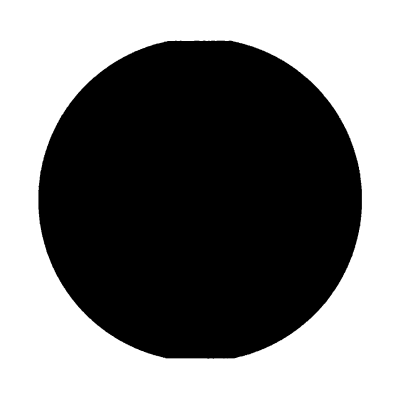

```mathematica
(*Import data*)
mask=Import[fNameMask,"Data"];
If[Length[Dimensions[mask]]>2,
mask=mask⟦All,All,2⟧;
,
mask=mask;
];
mask=Rescale[mask];
GraphicsRow[{HighlightImage[ImageAdjust[Image[im]],Image[mask]],Image[mask]}]
```

## 2.2. Downsample and selection of image part

```mathematica
(*Downsample by factor ds*)
ds=2;
```

```mathematica
(*Selection up to which pixel; here whole image*)
ySelect=Nx/ds;
```

### 2.2.0. Annotations

```mathematica
vesselAnnotations=vesselAnnotations/.("secondWall"->x_)->("secondWall"->x/ds);
vesselAnnotations=vesselAnnotations/.("firstWall"->x_)->("firstWall"->x/ds);
vesselAnnotationsData=vesselAnnotations/.("firstWall"->x_)->("firstWall"->Hold[Transpose@graphicsToImageCoordinates[Dimensions[im],Transpose@x]]);
vesselAnnotationsData=vesselAnnotationsData/.("secondWall"->x_)->("secondWall"->Hold[Transpose@graphicsToImageCoordinates[Dimensions[im],Transpose@x]]);
vesselAnnotationsData=vesselAnnotationsData//ReleaseHold;
```

### 2.2.1. Original image

```mathematica
(*Downsample*)
imOr=ImageData[ImageResize[Image[imOr],Round[Reverse[Dimensions[imOr]]/ds]]];
```

```mathematica
(*Select part of image*)
imOrhalf=imOr⟦1;;ySelect⟧;
```

### 2.2.2. Enhanced image

```mathematica
(*Downsample*)
im=ImageData[ImageResize[Image[im],Round[Reverse[Dimensions[im]]/ds]]];
```

```mathematica
Show[
ImageAdjust[Image[im]]
,
Graphics[Flatten@{Green,Line/@Transpose/@("firstWall"/.vesselAnnotations)}]
,
Graphics[Flatten@{Green,Line/@Transpose/@("secondWall"/.vesselAnnotations)}]
,ImageSize->400]
```

-Graphics-

```mathematica
(*Select part of image*)
imhalf=im⟦1;;ySelect⟧;
```

### 2.2.3. Mask

```mathematica
(*Downsample*)
mask=ImageData[ImageResize[Image[mask],Round[Reverse[Dimensions[mask]]/ds]]];
```

```mathematica
(*Select part of mask*)
maskhalf=mask⟦1;;ySelect⟧;
```

## 2.3 Enhanced + TV-flow image

```mathematica
os = OrientationScoreTransform[imhalf, "Orientations"-> No, "WaveletSize"-> 75];
```

```mathematica
Ds=1;
Da = 1/100;
t=0.5;
dt=t/5;
{leftTVF, leftTVFL1, leftTVFL2}=DoLeftTVF[os,1, t, dt, Ds, Da, Image@imhalf, 1];
```

```mathematica
imgLeftTVF = ImageClip[InverseOrientationScoreTransform[leftTVF]];
Image[imgLeftTVF, ImageSize->Scaled[0.5]]
```

-Graphics-

## 3. Parameters

```mathematica
(*Metric:*)
μ = .05;       (*Stiffness parameter*)
ϵ=10.;(*Anisotropy parameter (for sub-Riemannian case,epsilon->infty,(beta-)isotropic Riemannian case epsilon=1)*)

(*Volume/Image dimensions*)
{Nx,Ny}=Dimensions[imhalf];(*Number of pixels in x and y direction*)

(*Resolution parameters*)
periodicity = 2Pi;           (*Periodicity, =Pi (for theta from 0 to 1 Pi), or =2Pi (for theta from 0 to 2 Pi)*)
sθ = periodicity/No;  (*Angular resolution*)
```

## 3.1. Start- and endpoints

```mathematica
seedsFM={{197,289,(9 π)/16},{183,280,(3 π)/4},{176,277,(7 π)/8},{184,267,(7 π)/8},{174,238,(9 π)/8},{173,229,(5 π)/4},{208,218,(11 π)/8},{211,217,(25 π)/16},{260,288,(3 π)/8},{265,283,(3 π)/16},{277,261,0},{294,257,0},{268,240,(15 π)/8},{263,226,(13 π)/8},{249,232,(3 π)/2}};
```

```mathematica
tipsFM={{377,109,π},{390,109,(27 π)/16},{94,422,π/8},{194,356,(3 π)/16},{215.5,404.5,(3 π)/16},{185,465,π/16},{198,428,0},{46,349,(17 π)/16},{25,360,(13 π)/16},{9,313,(7 π)/8},{53,178,(21 π)/16},{7,221,(9 π)/8},{39,122,(5 π)/4},{54,100,(21 π)/16},{104,46,(3 π)/2},{94,57,(19 π)/16},{227,152,(3 π)/2},{131,36,(21 π)/16},{266,23,(13 π)/8},{320,502,π/2},{351,432,(11 π)/16},{310,422,(3 π)/4},{250,395,(11 π)/16},{421,400,(3 π)/16},{498,179,(31 π)/16},{456,151,0},{452,141,(27 π)/16},{468,269,0},{443,286,(9 π)/16},{445,427,(3 π)/8},{504,317,0},{457,101,(29 π)/16},{383,58,(5 π)/4},{311,9,(13 π)/8},{270,3,(11 π)/8},{241,30,(21 π)/16},{235,99,π},{257,122,(3 π)/2},{164.5,491.5,π/2},{125.5,472.5,(7 π)/8},{58.5,415.5,(11 π)/16},{11.5,193.5,(17 π)/16},{203.5,8.5,(25 π)/16},{371.5,32.5,(27 π)/16},{442.5,83.5,(13 π)/8}};
```

```mathematica
seedsPointFig={Green,PointSize[0.01],Point[imageToGraphicsCoordinates[{Nx,Ny},seedsFM[[All,;;2]]]]};
endsPointFig={Red,PointSize[0.01],Point[imageToGraphicsCoordinates[{Nx,Ny},tipsFM[[All,;;2]]]]};
```

## 3.2. Crossings and bifurcations

```mathematica
crossings=AutomaticCrossingIdentification[Select[vesselAnnotations,MemberQ[Flatten@Part[VesselTrees,rowSelection],"name"/.#]&]];
crossingsNew=ArrayReshape[DeleteCases[crossings,{}][[All,All,1]],{Dimensions[Flatten[DeleteCases[crossings,{}][[All,All,1]]]][[1]]/2,2}];
```

```mathematica
(*bifurcations*)
seedsIndex={{424,126},{328,144},{74,392},{167,305},{202,389},{198,288},{184,280},{143,451},{145,406},{176,277},{74,354},{77,356},{184,267},{84,300},{82,297},{112,283},{70,225},{174,238},{139,229},{71,144},{72,143},{142,227},{105,61},{102,63},{173,229},{208,218},{211,217},{188,90},{206,68},{191,91},{259,288},{265,283},{345,387},{343,386},{298,310},{271,260},{269,252},{267,240},{410,206},{426,136},{390,200},{446,268},{444,269},{410,208},{417,316},{421,314},{353,251},{352,247},{438,114},{436,112},{434,100},{294,38},{292,39},{263,226},{286,64},{279,102},{249,232},{262,199}};
```

## 3.3. Classification starting and end points for tracking per tree/type

```mathematica
startpointsTree={{1},{2},{3},{4},{5},{6},{7},{8},{9},{10},{11},{12},{13},{14},{15}};
endpointsTree={{5,39},{4,6,7,40},{3,8,41},{9,10,11,42},{12,13,14},{15,16},{18,(*19,*)43},{17},{20},{21,22,23},{24},{(*1,26,*)30,31,32,33,45},{25,(*27,*)28,29},{34,35,(*36,*)37},{(*2,*)38,44}};
```

```mathematica
(*first arteries, second veins*)
startpointsType={{1,3,5,7,9,11,13,15},{2,4,6,8,10,12,14}};
endpointsType={{5,39,3,8,41,12,13,14,18,(*19,*)43,20,24,25,(*27,*)28,29,(*2,*)38,44},{4,6,7,40,9,10,11,42,15,16,17,21,22,23,(*1,26,*)30,31,32,33,45,34,35,(*36,*)37}};
```

```mathematica
startpoints={{1},{2},{3},{4},{5},{6},{7},{8},{9},{10},{11},{12},{13},{14},{15}};
endpoints={{5,39},{4,6,7,40},{3,8,41},{9,10,11,42},{12,13,14},{15,16},{18,19,43},{17},{20},{21,22,23},{24},{1,26,30,31,32,33,45},{25,27,28,29},{34,35,36,37},{2,38,44}};
```

## 4a. Calculate data for tracking

## 4a.1. Parameters

```mathematica
(*Parameters to calculate data-driven term*)
ξ=1;
ζ=1;
σs=1.5;
σa=0.6;
```

```mathematica
(*Orientation Score of boarder*)
osGFBoarder=OrientationScoreTransform[Image@maskhalf,"Orientations"->No,"WaveletSize"->75,"InflectionPoint"->0.999,"OverlapFactor"->1];
```

```mathematica
(*Cost function C parameters: C=1/(1+λ V)^p; V Vesselness*)
λ=1000;
p=3;
```

```mathematica
(*ξ for tracking*)
xiLIF=(μ*ds)^-1;
```

## 4a.2. Data-driven term, Vesselness & Cost Function

### 4a.2.1. Original image

```mathematica
osGFOr=OrientationScoreTransform[Image@imOrhalf,"Orientations"->No,"WaveletSize"->75,"InflectionPoint"->0.999,"OverlapFactor"->1];
```

```mathematica
{gf1,oc1}=StabilizeGFandOC[osGFOr["FullData"],1,ξ,ζ,σs,σa];
{gf2,oc2}=StabilizeGFandOC[oc1,1,ξ,ζ,σs,σa];
{gf3,oc3}=StabilizeGFandOC[oc2,1,ξ,ζ,σs,σa];
GraphicsRow[Prepend[ArrayPlot[Map[Max,#,{2}],PlotRangePadding->None,Frame->False]&/@{oc1,oc2,oc3},Image@imOrhalf],ImageSize->Full]
```

{0.00124896,1.}

{0.0069161,1.}

{0.0232369,1.}

-Graphics-

```mathematica
(*Data-driven term*)
HoutOr=CalcGaugeFrameNew2[ObjPositionOrientationData[{"Data"->oc3,"Symmetry"->2π, "Wavelets"-> None, "InputData"-> None, "DcFilteredImage"->0}],1,ζ,σs,σa];
```

```mathematica
(*Vesselness*)
multiscalecostLIFExtRegOr=MultiScaleVesselnessExtReg[osGFOr["FullData"],osGFBoarder["FullData"],ξ,1,{1,1.5},"LIF",2,0];(*Left-Invariant Multiscale Cost of image without boarder*)
```

```mathematica
(*Cost Function*)
costOr=CostFunction[AddLifts[MultiScaleVesselnessFilter[Rescale@multiscalecostLIFExtRegOr],Map[#(*-{ySelect,0}*)&,seedsIndex]],λ,p];
```

### 4a.2.2. Enhanced image

```mathematica
osGFnoisy=OrientationScoreTransform[Image@imhalf,"Orientations"->No,"WaveletSize"->75,"InflectionPoint"->0.999,"OverlapFactor"->1];
```

```mathematica
{gf1,oc1}=StabilizeGFandOC[osGFnoisy["FullData"],1,ξ,ζ,σs,σa];
{gf2,oc2}=StabilizeGFandOC[oc1,1,ξ,ζ,σs,σa];
{gf3,oc3}=StabilizeGFandOC[oc2,1,ξ,ζ,σs,σa];
GraphicsRow[Prepend[ArrayPlot[Map[Max,#,{2}],PlotRangePadding->None,Frame->False]&/@{oc1,oc2,oc3},Image@imhalf],ImageSize->Full]
```

{0.00620975,1.}

{0.00690933,1.}

{0.0139527,1.}

-Graphics-

```mathematica
(*Data-driven term*)
Houtnoisy=CalcGaugeFrameNew2[ObjPositionOrientationData[{"Data"->oc3,"Symmetry"->2π, "Wavelets"-> None, "InputData"-> None, "DcFilteredImage"->0}],1,ζ,σs,σa];
```

```mathematica
(*Vesselness*)
multiscalecostLIFExtRegnoisy=MultiScaleVesselnessExtReg[osGFnoisy["FullData"],osGFBoarder["FullData"],ξ,1,{1,1.5},"LIF",2,0];(*Left-Invariant Multiscale Cost of image without boarder*)
```

```mathematica
(*Cost Function*)
costnoisy=CostFunction[AddLifts[MultiScaleVesselnessFilter[Rescale@multiscalecostLIFExtRegnoisy],Map[#(*-{ySelect,0}*)&,seedsIndex]],λ,p];
```

### 4a.2.3. Enhanced image + TV-Flow

```mathematica
{gf1,oc1}=StabilizeGFandOC[leftTVF["FullData"],1,ξ,ζ,σs,σa];
{gf2,oc2}=StabilizeGFandOC[oc1,1,ξ,ζ,σs,σa];
{gf3,oc3}=StabilizeGFandOC[oc2,1,ξ,ζ,σs,σa];
GraphicsRow[Prepend[ArrayPlot[Map[Max,#,{2}],PlotRangePadding->None,Frame->False]&/@{oc1,oc2,oc3},Image@imhalf],ImageSize->Full]
```

{0.00532355,1.}

{0.006599,1.}

{0.0107367,1.}

-Graphics-

```mathematica
(*Data-driven term*)
Hout=CalcGaugeFrameNew2[ObjPositionOrientationData[{"Data"->oc3,"Symmetry"->2π, "Wavelets"-> None, "InputData"-> None, "DcFilteredImage"->0}],1,ζ,σs,σa];
```

```mathematica
(*Vesselness*)
multiscalecostLIFExtReg=MultiScaleVesselnessExtReg[leftTVF["FullData"],osGFBoarder["FullData"],ξ,1,{1,1.5},"LIF",2,0];(*Left-Invariant Multiscale Cost of image without boarder*)
```

```mathematica
(*Cost Function*)
costTVF1=CostFunction[AddLifts[MultiScaleVesselnessFilter[Rescale@multiscalecostLIFExtReg],Map[#(*-{ySelect,0}*)&,seedsIndex]],λ,p];
```

## 4a.3. Metrics

```mathematica
γ=15;
```

### 4a.3.1. Original image

```mathematica
{MMixedOr,wOr}=metricMvectorwMixed[costOr,{ySelect,Ny,No},{1,0.1,xiLIF^2},{1,1,1},γ,Map[Transpose[Inverse[#]]&,HoutOr,{3}],crossingsNew,0.1,ySelect];
```

### 4a.3.2. Enhanced image

```mathematica
{MMixednoisy,wnoisy}=metricMvectorwMixed[costnoisy,{ySelect,Ny,No},{1,0.1,xiLIF^2},{1,1,1},γ,Map[Transpose[Inverse[#]]&,Houtnoisy,{3}],crossingsNew,0.1,ySelect];
```

### 4a.3.3. Enhanced image + TV-Flow

```mathematica
{MMixed,w}=metricMvectorwMixed[costTVF1,{ySelect,Ny,No},{1,0.1,xiLIF^2},{1,1,1},γ,Map[Transpose[Inverse[#]]&,Hout,{3}],crossingsNew,0.1,ySelect];
```

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.55576×10^9,1.84856×10^9,4.64774×10^7},{-1.04344×10^10,-1.23982×10^10,-3.11723×10^8},{1.51624×10^8,1.8016×10^8,4.52968×10^6}} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{-1.55576×10^9,-1.84856×10^9,-4.64774×10^7},{1.04344×10^10,1.23982×10^10,3.11723×10^8},{1.51624×10^8,1.8016×10^8,4.52968×10^6}} may contain significant numerical errors.

## 4a.4. Calculating geodesics

### 4a.4.1 Single Run

#### 4a.4.1.1. Original image

```mathematica
{HeightOr,geodesicsOr}=runReedsSheppForwardGFMultipleHeightGeos[{Nx,Ny,No},N[Transpose[MMixedOr,{3,4,5,1,2}]],N[wOr],N[{{0.5,Nx+0.5},{0.5,Ny+0.5},{0-sθ/2,2π-sθ/2}}],N[Map[#(*-{ySelect,0,0}*)&,seedsFM]],N[ Map[#&,tipsFM]],0.1,3];
```

Finished loading all data

metric (3, 3, 512, 512, 96)

w (3, 512, 512, 96)

Finished duplicating arrays and matrices to mirror angular periodicity

Data defined in Fast-Marching code

Field verbosity defaults to 1

Field order defaults to 1

Field seedRadius defaults to 0

Fast marching solver completed in 268.53 s.

Field geodesicSolver defaults to Discrete

Field geodesicStep defaults to 0.25

Field geodesicWeightThreshold defaults to 0.001

Field geodesicVolumeBound defaults to 10.985

Calculating paths and volume done

Selecting correct paths done

Done.

#### 4a.4.1.2. Enhanced image

```mathematica
{Heightnoisy,geodesicsnoisy}=runReedsSheppForwardGFMultipleHeightGeos[{Nx,Ny,No},N[Transpose[MMixednoisy,{3,4,5,1,2}]],N[wnoisy],N[{{0.5,Nx+0.5},{0.5,Ny+0.5},{0-sθ/2,2π-sθ/2}}],N[Map[#(*-{ySelect,0,0}*)&,seedsFM]],N[ Map[#&,tipsFM]],0.1,3];
```

Finished loading all data

metric (3, 3, 512, 512, 96)

w (3, 512, 512, 96)

Finished duplicating arrays and matrices to mirror angular periodicity

Data defined in Fast-Marching code

Field verbosity defaults to 1

Field order defaults to 1

Field seedRadius defaults to 0

Fast marching solver completed in 289.445 s.

Field geodesicSolver defaults to Discrete

Field geodesicStep defaults to 0.25

Field geodesicWeightThreshold defaults to 0.001

Field geodesicVolumeBound defaults to 10.985

Calculating paths and volume done

Selecting correct paths done

Done.

#### 4a.4.1.3. Enhanced image + TV-Flow

```mathematica
{Height,geodesicsTVF1}=runReedsSheppForwardGFMultipleHeightGeos[{Nx,Ny,No},N[Transpose[MMixed,{3,4,5,1,2}]],N[w],N[{{0.5,Nx+0.5},{0.5,Ny+0.5},{0-sθ/2,2π-sθ/2}}],N[Map[#(*-{ySelect,0,0}*)&,seedsFM]],N[ Map[#&,tipsFM]],0.1,3];
```

Finished loading all data

metric (3, 3, 512, 512, 96)

w (3, 512, 512, 96)

Finished duplicating arrays and matrices to mirror angular periodicity

Data defined in Fast-Marching code

Field verbosity defaults to 1

Field order defaults to 1

Field seedRadius defaults to 0

Fast marching solver completed in 296.402 s.

Field geodesicSolver defaults to Discrete

Field geodesicStep defaults to 0.25

Field geodesicWeightThreshold defaults to 0.001

Field geodesicVolumeBound defaults to 10.985

Calculating paths and volume done

Selecting correct paths done

Done.

### 4a.4.2. Per Type (Artery-Vein)

#### 4a.4.2.1. Original image

```mathematica
geodesicsVeinArteryOr={};
heightVeinArteryOr={};
```

```mathematica
For[i=1,i<=Length[startpointsType],i++,
Print["iteration ",i,"/",Length[startpointsType]];
{HeightVeinArtery,geodesicsVeinArtery}=runReedsSheppForwardGFMultipleHeightGeos[{Nx,Ny,No},N[Transpose[MMixedOr,{3,4,5,1,2}]],N[wOr],N[{{0.5,Nx+0.5},{0.5,Ny+0.5},{0-sθ/2,2π-sθ/2}}],N[Map[#(*-{ySelect,0,0}*)&,seedsFM[[startpointsType[[i]]]]]],N[ Map[#&,tipsFM[[endpointsType[[i]]]]]],0.1,3];
(*Export[StringJoin[exportfolder,"geodesicsOr_seed",ToString[i],".hdf"],Normal[geodesicsPerSeed]];*)
AppendTo[geodesicsVeinArteryOr,Normal[geodesicsVeinArtery]];
AppendTo[heightVeinArteryOr,Normal[HeightVeinArtery]];
]
```

#### 4a.4.2.2. Enhanced image

```mathematica
geodesicsVeinArterynoisy={};
heightVeinArterynoisy={};
```

```mathematica
For[i=1,i<=Length[startpointsType],i++,
Print["iteration ",i,"/",Length[startpointsType]];
{HeightVeinArtery,geodesicsVeinArtery}=runReedsSheppForwardGFMultipleHeightGeos[{Nx,Ny,No},N[Transpose[MMixednoisy,{3,4,5,1,2}]],N[wnoisy],N[{{0.5,Nx+0.5},{0.5,Ny+0.5},{0-sθ/2,2π-sθ/2}}],N[Map[#(*-{ySelect,0,0}*)&,seedsFM[[startpointsType[[i]]]]]],N[ Map[#&,tipsFM[[endpointsType[[i]]]]]],0.1,3];
(*Export[StringJoin[exportfolder,"geodesicsnoisy_seed",ToString[i],".hdf"],Normal[geodesicsPerSeed]];*)
AppendTo[geodesicsVeinArterynoisy,Normal[geodesicsVeinArtery]];
AppendTo[heightVeinArterynoisy,Normal[HeightVeinArtery]];
]
```

#### 4a.4.2.3. Enhanced image + TV-Flow

```mathematica
geodesicsVeinArteryTVF1={};
heightVeinArteryTVF1={};
```

```mathematica
For[i=1,i<=Length[startpointsType],i++,
Print["iteration ",i,"/",Length[startpointsType]];
{HeightVeinArtery,geodesicsVeinArtery}=runReedsSheppForwardGFMultipleHeightGeos[{Nx,Ny,No},N[Transpose[MMixed,{3,4,5,1,2}]],N[w],N[{{0.5,Nx+0.5},{0.5,Ny+0.5},{0-sθ/2,2π-sθ/2}}],N[Map[#(*-{ySelect,0,0}*)&,seedsFM[[startpointsType[[i]]]]]],N[ Map[#&,tipsFM[[endpointsType[[i]]]]]],0.1,3];
(*Export[StringJoin[exportfolder,"geodesicsTVF1_seed",ToString[i],".hdf"],Normal[geodesicsPerSeed]];*)
AppendTo[geodesicsVeinArteryTVF1,Normal[geodesicsVeinArtery]];
AppendTo[heightVeinArteryTVF1,Normal[HeightVeinArtery]];
]
```

iteration 1/2

Finished loading all data

metric (3, 3, 512, 512, 96)

w (3, 512, 512, 96)

Finished duplicating arrays and matrices to mirror angular periodicity

Data defined in Fast-Marching code

Field verbosity defaults to 1

Field order defaults to 1

Field seedRadius defaults to 0

Fast marching solver completed in 288.766 s.

Field geodesicSolver defaults to Discrete

Field geodesicStep defaults to 0.25

Field geodesicWeightThreshold defaults to 0.001

Field geodesicVolumeBound defaults to 10.985

Calculating paths and volume done

Selecting correct paths done

Done.

iteration 2/2

Finished loading all data

metric (3, 3, 512, 512, 96)

w (3, 512, 512, 96)

Finished duplicating arrays and matrices to mirror angular periodicity

Data defined in Fast-Marching code

Field verbosity defaults to 1

Field order defaults to 1

Field seedRadius defaults to 0

Fast marching solver completed in 303.452 s.

Field geodesicSolver defaults to Discrete

Field geodesicStep defaults to 0.25

Field geodesicWeightThreshold defaults to 0.001

Field geodesicVolumeBound defaults to 10.985

Calculating paths and volume done

Selecting correct paths done

Done.

### 4a.4.3. Per Seed

#### 4a.4.3.1. Original image

```mathematica
geodesicsAllOr={};
heightAllOr={};
```

```mathematica
For[i=1,i<=Length[startpointsTree],i++,
Print["iteration ",i,"/",Length[startpointsTree]];
{HeightPerSeed,geodesicsPerSeed}=runReedsSheppForwardGFMultipleHeightGeos[{Nx,Ny,No},N[Transpose[MMixedOr,{3,4,5,1,2}]],N[wOr],N[{{0.5,Nx+0.5},{0.5,Ny+0.5},{0-sθ/2,2π-sθ/2}}],N[Map[#(*-{ySelect,0,0}*)&,seedsFM[[startpointsTree[[i]]]]]],N[ Map[#&,tipsFMnew2[[endpointsTree[[i]]]]]],0.1,3];
(*Export[StringJoin[exportfolder,"geodesicsOr_seed",ToString[i],".hdf"],Normal[geodesicsPerSeed]];*)
AppendTo[geodesicsAllOr,Normal[geodesicsPerSeed]];
AppendTo[heightAllOr,Normal[HeightPerSeed]];
]
```

#### 4a.4.3.2. Enhanced image

```mathematica
geodesicsAllnoisy={};
heightAllnoisy={};
```

```mathematica
For[i=1,i<=Length[startpointsTree],i++,
Print["iteration ",i,"/",Length[startpointsTree]];
{HeightPerSeed,geodesicsPerSeed}=runReedsSheppForwardGFMultipleHeightGeos[{Nx,Ny,No},N[Transpose[MMixednoisy,{3,4,5,1,2}]],N[wnoisy],N[{{0.5,Nx+0.5},{0.5,Ny+0.5},{0-sθ/2,2π-sθ/2}}],N[Map[#(*-{ySelect,0,0}*)&,seedsFM[[startpointsTree[[i]]]]]],N[ Map[#&,tipsFM[[endpointsTree[[i]]]]]],0.1,3];
(*Export[StringJoin[exportfolder,"geodesicsnoisy_seed",ToString[i],".hdf"],Normal[geodesicsPerSeed]];*)
AppendTo[geodesicsAllnoisy,Normal[geodesicsPerSeed]];
AppendTo[heightAllnoisy,Normal[HeightPerSeed]];
]
```

#### 4a.4.3.3. Enhanced image + TV-Flow

```mathematica
geodesicsAllTVF1={};
heightAllTVF1={};
```

```mathematica
For[i=1,i<=Length[startpointsTree],i++,
Print["iteration ",i,"/",Length[startpointsTree]];
{HeightPerSeed,geodesicsPerSeed}=runReedsSheppForwardGFMultipleHeightGeos[{Nx,Ny,No},N[Transpose[MMixed,{3,4,5,1,2}]],N[w],N[{{0.5,Nx+0.5},{0.5,Ny+0.5},{0-sθ/2,2π-sθ/2}}],N[Map[#(*-{ySelect,0,0}*)&,seedsFM[[startpointsTree[[i]]]]]],N[ Map[#&,tipsFM[[endpointsTree[[i]]]]]],0.1,3];
(*Export[StringJoin[exportfolder,"geodesicsTVF1_seed",ToString[i],".hdf5"],Normal[geodesicsPerSeed]];*)
AppendTo[geodesicsAllTVF1,Normal[geodesicsPerSeed]];
AppendTo[heightAllTVF1,Normal[HeightPerSeed]];
]
```

iteration 1/15

Finished loading all data

metric (3, 3, 512, 512, 96)

w (3, 512, 512, 96)

Finished duplicating arrays and matrices to mirror angular periodicity

Data defined in Fast-Marching code

Field verbosity defaults to 1

Field order defaults to 1

Field seedRadius defaults to 0

Fast marching solver completed in 280.276 s.

Field geodesicSolver defaults to Discrete

Field geodesicStep defaults to 0.25

Field geodesicWeightThreshold defaults to 0.001

Field geodesicVolumeBound defaults to 10.985

Calculating paths and volume done

Selecting correct paths done

Done.

iteration 2/15

Finished loading all data

metric (3, 3, 512, 512, 96)

w (3, 512, 512, 96)

Finished duplicating arrays and matrices to mirror angular periodicity

Data defined in Fast-Marching code

Field verbosity defaults to 1

Field order defaults to 1

Field seedRadius defaults to 0

Fast marching solver completed in 285.466 s.

Field geodesicSolver defaults to Discrete

Field geodesicStep defaults to 0.25

Field geodesicWeightThreshold defaults to 0.001

Field geodesicVolumeBound defaults to 10.985

Calculating paths and volume done

Selecting correct paths done

Done.

iteration 3/15

Finished loading all data

metric (3, 3, 512, 512, 96)

w (3, 512, 512, 96)

Finished duplicating arrays and matrices to mirror angular periodicity

Data defined in Fast-Marching code

Field verbosity defaults to 1

Field order defaults to 1

Field seedRadius defaults to 0

Fast marching solver completed in 276.635 s.

Field geodesicSolver defaults to Discrete

Field geodesicStep defaults to 0.25

Field geodesicWeightThreshold defaults to 0.001

Field geodesicVolumeBound defaults to 10.985

Calculating paths and volume done

Selecting correct paths done

Done.

iteration 4/15

Finished loading all data

metric (3, 3, 512, 512, 96)

w (3, 512, 512, 96)

Finished duplicating arrays and matrices to mirror angular periodicity

Data defined in Fast-Marching code

Field verbosity defaults to 1

Field order defaults to 1

Field seedRadius defaults to 0

Fast marching solver completed in 278.856 s.

Field geodesicSolver defaults to Discrete

Field geodesicStep defaults to 0.25

Field geodesicWeightThreshold defaults to 0.001

Field geodesicVolumeBound defaults to 10.985

Calculating paths and volume done

Selecting correct paths done

Done.

iteration 5/15

Finished loading all data

metric (3, 3, 512, 512, 96)

w (3, 512, 512, 96)

Finished duplicating arrays and matrices to mirror angular periodicity

Data defined in Fast-Marching code

Field verbosity defaults to 1

Field order defaults to 1

Field seedRadius defaults to 0

Fast marching solver completed in 274.74 s.

Field geodesicSolver defaults to Discrete

Field geodesicStep defaults to 0.25

Field geodesicWeightThreshold defaults to 0.001

Field geodesicVolumeBound defaults to 10.985

Calculating paths and volume done

Selecting correct paths done

Done.

iteration 6/15

Finished loading all data

metric (3, 3, 512, 512, 96)

w (3, 512, 512, 96)

Finished duplicating arrays and matrices to mirror angular periodicity

Data defined in Fast-Marching code

Field verbosity defaults to 1

Field order defaults to 1

Field seedRadius defaults to 0

Fast marching solver completed in 270.609 s.

Field geodesicSolver defaults to Discrete

Field geodesicStep defaults to 0.25

Field geodesicWeightThreshold defaults to 0.001

Field geodesicVolumeBound defaults to 10.985

Calculating paths and volume done

Selecting correct paths done

Done.

iteration 7/15

Finished loading all data

metric (3, 3, 512, 512, 96)

w (3, 512, 512, 96)

Finished duplicating arrays and matrices to mirror angular periodicity

Data defined in Fast-Marching code

Field verbosity defaults to 1

Field order defaults to 1

Field seedRadius defaults to 0

Fast marching solver completed in 290.637 s.

Field geodesicSolver defaults to Discrete

Field geodesicStep defaults to 0.25

Field geodesicWeightThreshold defaults to 0.001

Field geodesicVolumeBound defaults to 10.985

Calculating paths and volume done

Selecting correct paths done

Done.

iteration 8/15

Finished loading all data

metric (3, 3, 512, 512, 96)

w (3, 512, 512, 96)

Finished duplicating arrays and matrices to mirror angular periodicity

Data defined in Fast-Marching code

Field verbosity defaults to 1

Field order defaults to 1

Field seedRadius defaults to 0

Fast marching solver completed in 278.468 s.

Field geodesicSolver defaults to Discrete

Field geodesicStep defaults to 0.25

Field geodesicWeightThreshold defaults to 0.001

Field geodesicVolumeBound defaults to 10.985

Calculating paths and volume done

Selecting correct paths done

Done.

iteration 9/15

Finished loading all data

metric (3, 3, 512, 512, 96)

w (3, 512, 512, 96)

Finished duplicating arrays and matrices to mirror angular periodicity

Data defined in Fast-Marching code

Field verbosity defaults to 1

Field order defaults to 1

Field seedRadius defaults to 0

Fast marching solver completed in 278.475 s.

Field geodesicSolver defaults to Discrete

Field geodesicStep defaults to 0.25

Field geodesicWeightThreshold defaults to 0.001

Field geodesicVolumeBound defaults to 10.985

Calculating paths and volume done

Selecting correct paths done

Done.

iteration 10/15

Finished loading all data

metric (3, 3, 512, 512, 96)

w (3, 512, 512, 96)

Finished duplicating arrays and matrices to mirror angular periodicity

Data defined in Fast-Marching code

Field verbosity defaults to 1

Field order defaults to 1

Field seedRadius defaults to 0

Fast marching solver completed in 281.466 s.

Field geodesicSolver defaults to Discrete

Field geodesicStep defaults to 0.25

Field geodesicWeightThreshold defaults to 0.001

Field geodesicVolumeBound defaults to 10.985

Calculating paths and volume done

Selecting correct paths done

Done.

iteration 11/15

Finished loading all data

metric (3, 3, 512, 512, 96)

w (3, 512, 512, 96)

Finished duplicating arrays and matrices to mirror angular periodicity

Data defined in Fast-Marching code

Field verbosity defaults to 1

Field order defaults to 1

Field seedRadius defaults to 0

Fast marching solver completed in 271.144 s.

Field geodesicSolver defaults to Discrete

Field geodesicStep defaults to 0.25

Field geodesicWeightThreshold defaults to 0.001

Field geodesicVolumeBound defaults to 10.985

Calculating paths and volume done

Selecting correct paths done

Done.

iteration 12/15

Finished loading all data

metric (3, 3, 512, 512, 96)

w (3, 512, 512, 96)

Finished duplicating arrays and matrices to mirror angular periodicity

Data defined in Fast-Marching code

Field verbosity defaults to 1

Field order defaults to 1

Field seedRadius defaults to 0

Fast marching solver completed in 270.14 s.

Field geodesicSolver defaults to Discrete

Field geodesicStep defaults to 0.25

Field geodesicWeightThreshold defaults to 0.001

Field geodesicVolumeBound defaults to 10.985

Calculating paths and volume done

Selecting correct paths done

Done.

iteration 13/15

Finished loading all data

metric (3, 3, 512, 512, 96)

w (3, 512, 512, 96)

Finished duplicating arrays and matrices to mirror angular periodicity

Data defined in Fast-Marching code

Field verbosity defaults to 1

Field order defaults to 1

Field seedRadius defaults to 0

Fast marching solver completed in 274.015 s.

Field geodesicSolver defaults to Discrete

Field geodesicStep defaults to 0.25

Field geodesicWeightThreshold defaults to 0.001

Field geodesicVolumeBound defaults to 10.985

Calculating paths and volume done

Selecting correct paths done

Done.

iteration 14/15

Finished loading all data

metric (3, 3, 512, 512, 96)

w (3, 512, 512, 96)

Finished duplicating arrays and matrices to mirror angular periodicity

Data defined in Fast-Marching code

Field verbosity defaults to 1

Field order defaults to 1

Field seedRadius defaults to 0

Fast marching solver completed in 272.03 s.

Field geodesicSolver defaults to Discrete

Field geodesicStep defaults to 0.25

Field geodesicWeightThreshold defaults to 0.001

Field geodesicVolumeBound defaults to 10.985

Calculating paths and volume done

Selecting correct paths done

Done.

iteration 15/15

Finished loading all data

metric (3, 3, 512, 512, 96)

w (3, 512, 512, 96)

Finished duplicating arrays and matrices to mirror angular periodicity

Data defined in Fast-Marching code

Field verbosity defaults to 1

Field order defaults to 1

Field seedRadius defaults to 0

Fast marching solver completed in 273.29 s.

Field geodesicSolver defaults to Discrete

Field geodesicStep defaults to 0.25

Field geodesicWeightThreshold defaults to 0.001

Field geodesicVolumeBound defaults to 10.985

Calculating paths and volume done

Selecting correct paths done

Done.

## 4a.5. Export geodesics

```mathematica
(*define the basis folder from which all folders can be created and reached*)
basisfolderExport=FileNameJoin[{NotebookDirectory[],"Geodesics"}];
(*define the export folder*)
dataexportfolder=FileNameJoin[{basisfolderExport,FileBaseName[FileNames["*.png",directory][[imNr]]],"lambda 3 p 1000"}];
```

### 4a.5.1. One Run

```mathematica
Export[FileNameJoin[{dataexportfolder,"geodesicsOr.dat"}],Normal@geodesicsOr,"Table"];
```

```mathematica
Export[FileNameJoin[{dataexportfolder,"geodesicsnoisy.dat"}],Normal@geodesicsnoisy,"Table"];
```

```mathematica
Export[FileNameJoin[{dataexportfolder,"geodesicsTVF1.dat"}],Normal@geodesicsTVF1,"Table"];
```

### 4a.5.2. Per Type (Artery-Vein)

```mathematica
Export[FileNameJoin[{dataexportfolder,"geodesicsVeinArteryOr.dat"}],Normal@geodesicsVeinArteryOr,"Table"];
```

```mathematica
Export[FileNameJoin[{dataexportfolder,"geodesicsVeinArterynoisy.dat"}],Normal@geodesicsVeinArterynoisy,"Table"];
```

```mathematica
Export[FileNameJoin[{dataexportfolder,"geodesicsVeinArteryTVF1.dat"}],Normal@geodesicsVeinArteryTVF1,"Table"];
```

### 4a.5.3. Per Seed

```mathematica
Export[FileNameJoin[{dataexportfolder,"geodesicsAllOr.dat"}],Normal@geodesicsAllOr,"Table"];
```

```mathematica
Export[FileNameJoin[{dataexportfolder,"geodesicsAllnoisy.dat"}],Normal@geodesicsAllnoisy,"Table"];
```

```mathematica
Export[FileNameJoin[{dataexportfolder,"geodesicsAllTVF1.dat"}],Normal@geodesicsAllTVF1,"Table"];
```

## 4b. Load geodesics

```mathematica
(*define the basis folder from which all exported geodesics can be imported*)
basisfolderExport=FileNameJoin[{NotebookDirectory[],"Geodesics"}];
dataexportfolder=FileNameJoin[{basisfolderExport,FileBaseName[FileNames["*.png",directory][[imNr]]]}];
```

## 4b.1. Single Run

### 4b.1.1. Original image

```mathematica
geodesicsOr=ToExpression[Import[FileNameJoin[{dataexportfolder,"lambda 3 p 1000","geodesicsOr.dat"}],"TSV"]];
```

### 4b.1.2. Enhanced image

```mathematica
geodesicsnoisy=ToExpression[Import[FileNameJoin[{dataexportfolder,"lambda 3 p 1000","geodesicsnoisy.dat"}],"TSV"]];
```

### 4b.1.3. Enhanced image + TV-Flow

```mathematica
geodesicsTVF1=ToExpression[Import[FileNameJoin[{dataexportfolder,"lambda 3 p 1000","geodesicsTVF1.dat"}],"TSV"]];
```

## 4b.2. Per Type (Artery-Vein)

### 4b.2.1. Original image

```mathematica
geodesicsVeinArteryOr=ToExpression[Import[FileNameJoin[{dataexportfolder,"lambda 3 p 1000","geodesicsVeinArteryOr.dat"}],"TSV"]];
```

### 4b.2.2. Enhanced image

```mathematica
geodesicsVeinArterynoisy=ToExpression[Import[FileNameJoin[{dataexportfolder,"lambda 3 p 1000","geodesicsVeinArterynoisy.dat"}],"TSV"]];
```

### 4b.2.3. Enhanced image + TV-Flow

```mathematica
geodesicsVeinArteryTVF1=ToExpression[Import[FileNameJoin[{dataexportfolder,"lambda 3 p 1000","geodesicsVeinArteryTVF1.dat"}],"TSV"]];
```

## 4b.3. Per Seed

```mathematica
(*Export[StringJoin[dataexportfolder,"lambda 2.5 p 1000//","geodesicsAllOr.dat"],Map[graphicsToImageCoordinates[imhalf,#[[1]]]&,endtracksFigMixedFGSeedTipOr[[2;;]]],"Table"];*)
```

### 4b.3.1. Original image

```mathematica
geodesicsAllOr=ToExpression[Import[FileNameJoin[{dataexportfolder,"lambda 3 p 1000","geodesicsAllOr.dat"}],"TSV"]];
```

### 4b.3.2. Enhanced image

```mathematica
geodesicsAllnoisy=ToExpression[Import[FileNameJoin[{dataexportfolder,"lambda 3 p 1000","geodesicsAllnoisy.dat"}],"TSV"]];
```

### 4b.3.3. Enhanced image + TV-Flow

```mathematica
geodesicsAllTVF1=ToExpression[Import[FileNameJoin[{dataexportfolder,"lambda 3 p 1000","geodesicsAllTVF1.dat"}],"TSV"]];
```

## 5. Visualization

## 5.1. Single Run

### 5.1.1. Original Image

```mathematica
endtracksFigMixedFGSeedTipOr=Flatten@{Cyan,LineImageCoordinates[imhalf,#⟦All,1;;2⟧]&/@Normal[geodesicsOr]};
```

```mathematica
GraphicsGrid[{{Image@imOrhalf,Show[Image@imOrhalf,Graphics[{seedsPointFig,endsPointFig,{Thickness[.003],endtracksFigMixedFGSeedTipOr}}]]}},ImageSize->600]
```

-Graphics-

### 5.1.2. Enhanced Image

```mathematica
endtracksFigMixedFGSeedTipnoisy=Flatten@{Cyan,LineImageCoordinates[imhalf,#⟦All,1;;2⟧]&/@Normal[geodesicsnoisy]};
```

```mathematica
GraphicsGrid[{{Image@imhalf,Show[Image@imhalf,Graphics[{seedsPointFig,{endsPointFig},{Thickness[.003],endtracksFigMixedFGSeedTipnoisy}}]]}},ImageSize->600]
```

-Graphics-

### 5.1.3. Enhanced Image + TV-flow

```mathematica
endtracksFigMixedFGSeedTipTVF1=Flatten@{Cyan,LineImageCoordinates[imhalf,#⟦All,1;;2⟧]&/@Normal[geodesicsTVF1]};
```

```mathematica
GraphicsGrid[{{Image@imgLeftTVF,Show[Image@imgLeftTVF,Graphics[{seedsPointFig,{endsPointFig},{Thickness[.003],endtracksFigMixedFGSeedTipTVF1}}]]}},ImageSize->600]
```

-Graphics-

## 5.2. Per Type (Artery-Vein)

### 5.2.1. Original Image

```mathematica
endtracksFigMixedFGArteryVeinOr=Map[{#[[1]],LineImageCoordinates[imhalf,#⟦All,1;;2⟧]&/@#[[2]]}&,Transpose[{{White,Cyan},geodesicsVeinArteryOr}],{1}];
```

```mathematica
GraphicsGrid[{{Image@imOrhalf,Show[Image@imOrhalf,Graphics[{seedsPointFig,{endsPointFig},{Thickness[.003],endtracksFigMixedFGArteryVeinOr}}]]}},ImageSize->600]
```

-Graphics-

### 5.2.2. Enhanced Image

```mathematica
endtracksFigMixedFGArteryVeinNoisy=Map[{#[[1]],LineImageCoordinates[imhalf,#⟦All,1;;2⟧]&/@#[[2]]}&,Transpose[{{White,Cyan},geodesicsVeinArterynoisy}],{1}];
```

```mathematica
GraphicsGrid[{{Image@imhalf,Show[Image@imhalf,Graphics[{seedsPointFig,{endsPointFig},{Thickness[.003],endtracksFigMixedFGArteryVeinNoisy}}]]}},ImageSize->600]
```

-Graphics-

### 5.2.3. Enhanced Image + TV-flow

```mathematica
endtracksFigMixedFGArteryVeinTVF1=Map[{#[[1]],LineImageCoordinates[imhalf,#⟦All,1;;2⟧]&/@#[[2]]}&,Transpose[{{White,Cyan},geodesicsVeinArteryTVF1}],{1}];
```

```mathematica
GraphicsGrid[{{Image@imgLeftTVF,Show[Image@imgLeftTVF,Graphics[{seedsPointFig,{endsPointFig},{Thickness[.003],endtracksFigMixedFGArteryVeinTVF1}}]]}},ImageSize->600]
```

-Graphics-

## 5.3. Per Seed

### 5.3.1. Original Image

```mathematica
endtracksFigMixedFGperSeedOr=Map[{#[[1]],LineImageCoordinates[imhalf,#⟦All,1;;2⟧]&/@#[[2]]}&,Transpose[{Lighter@ColorData[54,"ColorList"][[;;Length[startpointsTree]]],geodesicsAllOr}],{1}];
```

```mathematica
GraphicsGrid[{{Image@imOrhalf,Show[Image@imOrhalf,Graphics[{seedsPointFig,endsPointFig,{Thickness[.003],endtracksFigMixedFGperSeedOr}}]]}},ImageSize->600]
```

-Graphics-

### 5.3.2. Enhanced Image

```mathematica
endtracksFigMixedFGperSeedNoisy=Map[{#[[1]],LineImageCoordinates[imhalf,#⟦All,1;;2⟧]&/@#[[2]]}&,Transpose[{ColorData[54,"ColorList"][[;;Length[startpointsTree]]],geodesicsAllnoisy}],{1}];
```

```mathematica
GraphicsGrid[{{Image@imhalf,Show[Image@imhalf,Graphics[{seedsPointFig,{endsPointFig},{Thickness[.003],endtracksFigMixedFGperSeedNoisy}}]]}},ImageSize->600]
```

-Graphics-

### 5.3.3. Enhanced Image + TV-flow

```mathematica
endtracksFigMixedFGperSeedTVF1=Map[{#[[1]],LineImageCoordinates[imhalf,#⟦All,1;;2⟧]&/@#[[2]]}&,Transpose[{ColorData[54,"ColorList"][[;;Length[startpointsTree]]],geodesicsAllTVF1}],{1}];
```

```mathematica
GraphicsGrid[{{Image@imgLeftTVF,Show[Image@imgLeftTVF,Graphics[{seedsPointFig,{endsPointFig},{Thickness[.003],endtracksFigMixedFGperSeedTVF1}}]]}},ImageSize->600]
```

-Graphics-

## 6. Accuracy

```mathematica
a=Position[endpoints,#]&/@Range[Max[endpoints]];
```

## 5.1. Single Run

```mathematica
Manipulate[GraphicsRow[{Show[Image@imhalf,Graphics[{(*vesselTreeFig,*)seedsPointFig,endsPointFig,{Thickness[.003],endtracksFigMixedFGSeedTipnoisy[[1]],endtracksFigMixedFGSeedTipOr[[i+1]]}}]],Show[Image@imhalf,Graphics[{(*vesselTreeFig,*)seedsPointFig,endsPointFig,{Thickness[.003],endtracksFigMixedFGSeedTipnoisy[[1]],endtracksFigMixedFGSeedTipnoisy[[i+1]]}}]],Show[Image@imhalf,Graphics[{(*vesselTreeFig,*)seedsPointFig,endsPointFig,{Thickness[.003],endtracksFigMixedFGSeedTipnoisy[[1]],endtracksFigMixedFGSeedTipTVF1[[i+1]]}}]],Show[Image@imhalf,Graphics[{(*vesselTreeFig,*)seedsPointFig,endsPointFig}]]},ImageSize->Full],{i,1,Length[endtracksFigMixedFGSeedTipnoisy]-1,1}]
```

### 5.1.1. Original image

```mathematica
wrong=ConstantArray[0,Length[tipsFM]]; (*Assume all vessels are tracked correctly*)
wrong[[{3,12,18,23,25,28,29,33,38,39,41,44}]]=1; (*Indicate which vessels are tracked incorrectly*)
Total[wrong]
N[Total[(1-(Norm[tipsFM[[Flatten@endpoints]][[#,;;2]]-seedsFM[[Flatten@startpoints[[Flatten@a[[;;,;;,1]]]]]][[#,;;2]]]&/@Range[Length[tipsFM]])/Norm[{Nx,Ny}])*wrong]/(Length[tipsFM]-6) ](*Calculate 'correctness percentage'*)
```

12

0.226537

### 5.1.2. Enhanced image

```mathematica
wrong=ConstantArray[0,Length[tipsFM]]; (*Assume all vessels are tracked correctly*)
wrong[[{11,12,20,39,44}]]=1; (*Indicate which vessels are tracked incorrectly*)
Total[wrong]
N[Total[(1-(Norm[tipsFM[[Flatten@endpoints]][[#,;;2]]-seedsFM[[Flatten@startpoints[[Flatten@a[[;;,;;,1]]]]]][[#,;;2]]]&/@Range[Length[tipsFM]])/Norm[{Nx,Ny}])*wrong]/(Length[tipsFM]-6) ](*Calculate 'correctness percentage'*)
```

5

0.0930169

### 5.1.3. Enhanced image + TV-Flow

```mathematica
wrong=ConstantArray[0,Length[tipsFM]]; (*Assume all vessels are tracked correctly*)
wrong[[{11,12,44}]]=1; (*Indicate which vessels are tracked incorrectly*)
Total[wrong]
N[Total[(1-(Norm[tipsFM[[Flatten@endpoints]][[#,;;2]]-seedsFM[[Flatten@startpoints[[Flatten@a[[;;,;;,1]]]]]][[#,;;2]]]&/@Range[Length[tipsFM]])/Norm[{Nx,Ny}])*wrong]/(Length[tipsFM]-6) ](*Calculate 'correctness percentage'*)
```

3

0.0618271

## 5.2. Per Type (Artery-Vein)

```mathematica
Manipulate[GraphicsRow[{Show[Image@imhalf,Graphics[{(*vesselTreeFig,*)seedsPointFig,endsPointFig,{Thickness[.003],Cyan,endtracksFigMixedFGArteryVeinOr[[(Position[endpointsType,#]&/@Range[Length[tipsFM]])[[i,1,1]],2,(Position[endpointsType,#]&/@Range[Length[tipsFM]])[[i,1,2]]]]}}]],
Show[Image@imhalf,Graphics[{(*vesselTreeFig,*)seedsPointFig,endsPointFig,{Thickness[.003],Cyan,endtracksFigMixedFGArteryVeinNoisy[[(Position[endpointsType,#]&/@Range[Length[tipsFM]])[[i,1,1]],2,(Position[endpointsType,#]&/@Range[Length[tipsFM]])[[i,1,2]]]]}}]],
Show[Image@imhalf,Graphics[{(*vesselTreeFig,*)seedsPointFig,endsPointFig,{Thickness[.003],Cyan,endtracksFigMixedFGArteryVeinTVF1[[(Position[endpointsType,#]&/@Range[Length[tipsFM]])[[i,1,1]],2,(Position[endpointsType,#]&/@Range[Length[tipsFM]])[[i,1,2]]]]}}]](*,
Show[Image@imhalf,Graphics[{(*vesselTreeFig,*)seedsPointFig,endsPointFig}]]*)},ImageSize->Full],{i,1,Length[endtracksFigMixedFGSeedTipnoisy]-1,1}]
```

### 5.2.1. Original image

```mathematica
(*Original image*)
wrong=ConstantArray[0,Length[tipsFM]]; (*Assume all vessels are tracked correctly*)
wrong[[{12,23,33,38,39}]]=1; (*Indicate which vessels are tracked incorrectly*)
Total[wrong]
N[Total[(1-(Norm[tipsFM[[Flatten@endpoints]][[#,;;2]]-seedsFM[[Flatten@startpoints[[Flatten@a[[;;,;;,1]]]]]][[#,;;2]]]&/@Range[Length[tipsFM]])/Norm[{Nx,Ny}])*wrong]/(Length[tipsFM]-3) ](*Calculate 'correctness percentage'*)
```

5

0.0834506

### 5.2.2. Enhanced image

```mathematica
(*Noisy image*)
wrong=ConstantArray[0,Length[tipsFM]]; (*Assume all vessels are tracked correctly*)
wrong[[{}]]=1; (*Indicate which vessels are tracked incorrectly*)
Total[wrong]
N[Total[(1-(Norm[tipsFM[[Flatten@endpoints]][[#,;;2]]-seedsFM[[Flatten@startpoints[[Flatten@a[[;;,;;,1]]]]]][[#,;;2]]]&/@Range[Length[tipsFM]])/Norm[{Nx,Ny}])*wrong]/(Length[tipsFM]-3) ](*Calculate 'correctness percentage'*)
```

0

0.

### 5.2.3. Enhanced image + TV-Flow

```mathematica
(*TVF image*)
wrong=ConstantArray[0,Length[tipsFM]]; (*Assume all vessels are tracked correctly*)
wrong[[{}]]=1; (*Indicate which vessels are tracked incorrectly*)
Total[wrong]
N[Total[(1-(Norm[tipsFM[[Flatten@endpoints]][[#,;;2]]-seedsFM[[Flatten@startpoints[[Flatten@a[[;;,;;,1]]]]]][[#,;;2]]]&/@Range[Length[tipsFM]])/Norm[{Nx,Ny}])*wrong]/(Length[tipsFM]-3) ](*Calculate 'correctness percentage'*)
```

0

0.

## 5.3. Per Seed

```mathematica
Manipulate[GraphicsRow[{Show[Image@imhalf,Graphics[{(*vesselTreeFig,*)seedsPointFig,endsPointFig,{Thickness[.003],Cyan,endtracksFigMixedFGperSeedOr[[(Position[endpointsTree,#]&/@Range[Length[tipsFM]])[[i,1,1]],2,(Position[endpointsTree,#]&/@Range[Length[tipsFM]])[[i,1,2]]]]}}]],
Show[Image@imhalf,Graphics[{(*vesselTreeFig,*)seedsPointFig,endsPointFig,{Thickness[.003],Cyan,endtracksFigMixedFGperSeedNoisy[[(Position[endpointsTree,#]&/@Range[Length[tipsFM]])[[i,1,1]],2,(Position[endpointsTree,#]&/@Range[Length[tipsFM]])[[i,1,2]]]]}}]],
Show[Image@imhalf,Graphics[{(*vesselTreeFig,*)seedsPointFig,endsPointFig,{Thickness[.003],Cyan,endtracksFigMixedFGperSeedTVF1[[(Position[endpointsTree,#]&/@Range[Length[tipsFM]])[[i,1,1]],2,(Position[endpointsTree,#]&/@Range[Length[tipsFM]])[[i,1,2]]]]}}]]
},ImageSize->Full],{i,1,Length[endtracksFigMixedFGSeedTipnoisy]-1,1}]
```

### 5.3.1. Original image

```mathematica
wrong=ConstantArray[0,Length[tipsFM]]; (*Assume all vessels are tracked correctly*)
wrong[[{23,38,39}]]=1; (*Indicate which vessels are tracked incorrectly*)
Total[wrong]
N[Total[(1-(Norm[tipsFM[[Flatten@endpoints]][[#,;;2]]-seedsFM[[Flatten@startpoints[[Flatten@a[[;;,;;,1]]]]]][[#,;;2]]]&/@Range[Length[tipsFM]])/Norm[{Nx,Ny}])*wrong]/(Length[tipsFM]-6) ](*Calculate 'correctness percentage'*)
```

3

0.0510902

### 5.3.2. Enhanced image

```mathematica
wrong=ConstantArray[0,Length[tipsFM]]; (*Assume all vessels are tracked correctly*)
wrong[[{}]]=1; (*Indicate which vessels are tracked incorrectly*)
Total[wrong]
N[Total[(1-(Norm[tipsFM[[Flatten@endpoints]][[#,;;2]]-seedsFM[[Flatten@startpoints[[Flatten@a[[;;,;;,1]]]]]][[#,;;2]]]&/@Range[Length[tipsFM]])/Norm[{Nx,Ny}])*wrong]/(Length[tipsFM]-6) ](*Calculate 'correctness percentage'*)
```

0

0.

### 5.3.3. Enhanced image + TV-Flow

```mathematica
wrong=ConstantArray[0,Length[tipsFM]]; (*Assume all vessels are tracked correctly*)
wrong[[{}]]=1; (*Indicate which vessels are tracked incorrectly*)
Total[wrong]
N[Total[(1-(Norm[tipsFM[[Flatten@endpoints]][[#,;;2]]-seedsFM[[Flatten@startpoints[[Flatten@a[[;;,;;,1]]]]]][[#,;;2]]]&/@Range[Length[tipsFM]])/Norm[{Nx,Ny}])*wrong]/(Length[tipsFM]-6) ](*Calculate 'correctness percentage'*)
```

0

0.